# Hybrid fitness in Haploids

```mathematica
(*Parameter settings & Read file*)
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
pop1=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r=0.04_pop1_0.dat"];
pop2=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r=0.04_pop2_0.dat"];
```

```mathematica
(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
(*fixation during adaptive phase*)
Length@TakeWhile[Sign[slistpop1],#>0.5&];
Length@TakeWhile[Sign[slistpop2],#>0.5&];
(*fixation during adaptive phase & circling optimum*)
2*Length@TakeWhile[Sign[slistpop1],#>0.5&];
2*Length@TakeWhile[Sign[slistpop2],#>0.5&];
(*Renewal slist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;2*Length@TakeWhile[Sign[slistpop1],#>0.5&];;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;2*Length@TakeWhile[Sign[slistpop2],#>0.5&];;1]];
Length@slistpop1
Length@slistpop2
```

184

176

```mathematica
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;2*Length@TakeWhile[Sign[slistpop1],#>0.5&];;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;2*Length@TakeWhile[Sign[slistpop2],#>0.5&];;1]];
```

## Fitness within the population

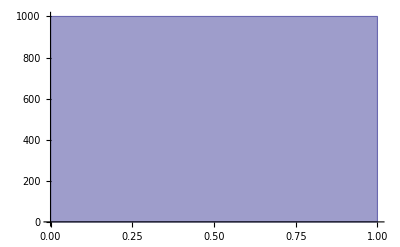

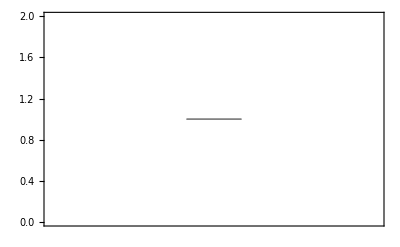

```mathematica
Pop1fitness={};
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
inter=Intersection[mutpop1,mutpop1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop1,mutpop1],Intersection[mutpop1,mutpop1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop1offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop1offspring,1]];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
]

Histogram[{Pop1fitness}]
BoxWhiskerChart[{Pop1fitness}]
```

## F1 fitness

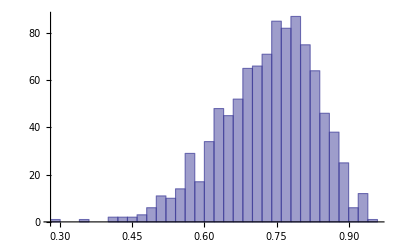

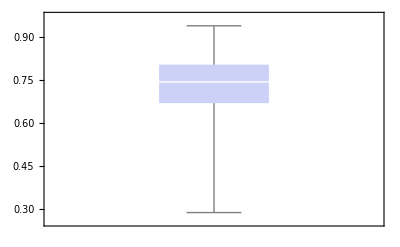

```mathematica
F1fitness={};
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];(*Calculating fitness of F1*)
];
Histogram[{F1fitness}]
BoxWhiskerChart[{F1fitness}]
```

## F2 fitness

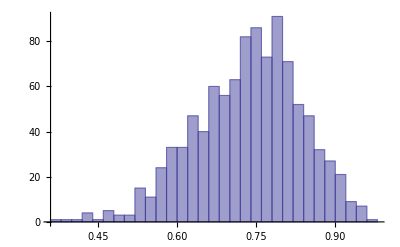

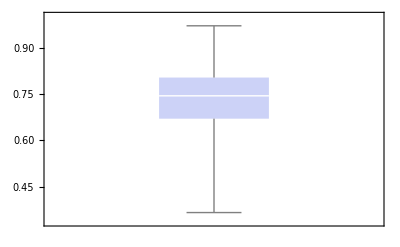

```mathematica
F2fitness={};
For[i=1,i≤1000,i++,
(*Making 2 F1 hybrids*)
F1hybrid1={};
F1hybrid2={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop2[[j]]]];
];

(*Making F2 hybrid*)
F2hybrid={};
inter=Intersection[F1hybrid1,F1hybrid2];(*mutations shared in both hybrids*)
comp=Complement[Union[F1hybrid1,F1hybrid2],Intersection[F1hybrid1,F1hybrid2]];(*mutations included in either hybrid*)
AppendTo[F2hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[F2hybrid,comp[[j]]]];
];

(*Calculating fitness of F2*)
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
]

Histogram[{F2fitness}]
BoxWhiskerChart[{F2fitness}]
```

## Backcross fitness (pop1 * F1)

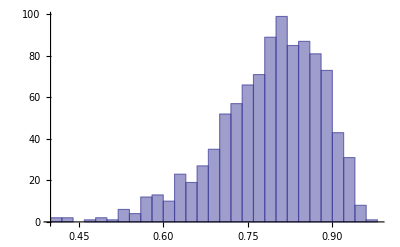

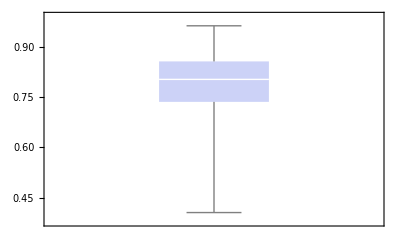

```mathematica
BC1fitness={};
For[i=1,i≤1000,i++,
(*Making F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC1 hybrid*)
BC1hybrid={};
inter=Intersection[F1hybrid1,mutpop1];
comp=Complement[Union[F1hybrid1,mutpop1],Intersection[F1hybrid1,mutpop1]];
AppendTo[BC1hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BC1hybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BC1hybrid];
AppendTo[BC1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
]

Histogram[{BC1fitness}]
BoxWhiskerChart[{BC1fitness}]
```

{0.998847,0.732764,0.735333,0.788355}

{1.49955×10^-14,0.0990364,0.100189,0.0921965}

{0.998847→1.49955×10^-14,0.732764→0.0990364,0.735333→0.100189,0.788355→0.0921965}

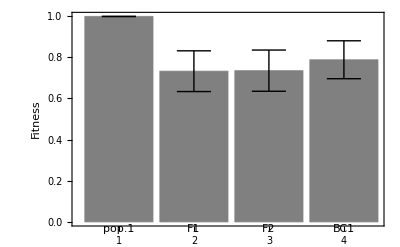

```mathematica
file={Pop1fitness,F1fitness,F2fitness,BC1fitness};
Meandata=Mean/@file
standardDev[data_]:=StandardDeviation[data]
stddevData=standardDev/@file
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
chartData=Table[Meandata[[i]]->stddevData[[i]],{i,1,Length[Meandata]}]
labels={"pop.1","F1","F2","BC1"};
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->labels,Frame->Left,FrameLabel->{None,Style["Fitness"]},ChartStyle->{Gray}]
```

# Hybrid fitness in diploids

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)

pop1=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r=0.04_pop1_0.dat"];
pop2=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r=0.04_pop2_0.dat"];
```

```mathematica
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
(*fixation during adaptive phase*)
Length@TakeWhile[Sign[slistpop1],#>0.5&];
Length@TakeWhile[Sign[slistpop2],#>0.5&];
(*fixation during adaptive phase & circling optimum*)
2*Length@TakeWhile[Sign[slistpop1],#>0.5&];
2*Length@TakeWhile[Sign[slistpop2],#>0.5&];
(*Renewal slist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;2*Length@TakeWhile[Sign[slistpop1],#>0.5&];;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;2*Length@TakeWhile[Sign[slistpop2],#>0.5&];;1]];
Length@slistpop1
Length@slistpop2
```

184

204

```mathematica
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;2*Length@TakeWhile[Sign[slistpop1],#>0.5&];;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;2*Length@TakeWhile[Sign[slistpop2],#>0.5&];;1]];
```

## Fitness within the population

```mathematica
Pop1fitness={};
gamete1=mutpop1/2;
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
(*Calculating fitness of offspring*)
cur=Total[Pop1offspring];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
]

Histogram[{Pop1fitness}]
BoxWhiskerChart[{Pop1fitness}]
```

-Graphics-

-Graphics-

## F1 fitness

-Graphics-

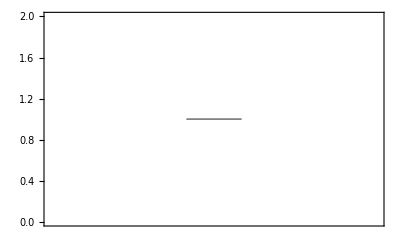

```mathematica
F1fitness={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
cur=Total[Join[gamete1,gamete2]];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];(*Calculating fitness of F1*)
];
Histogram[{F1fitness}]
BoxWhiskerChart[{F1fitness}]
```

## F2 fitness

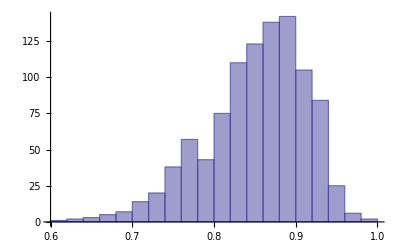

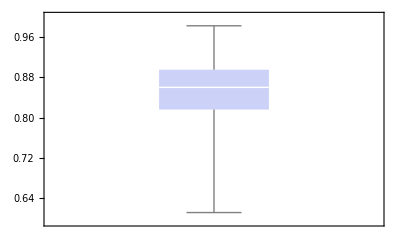

```mathematica
F2fitness={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
F2hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete1[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete2[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete2[[j]]]];
];
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
]
Histogram[{F2fitness}]
BoxWhiskerChart[{F2fitness}]
```

## Backcross fitness (pop1 * F1)

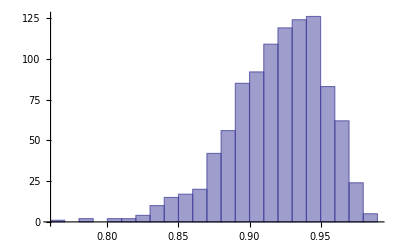

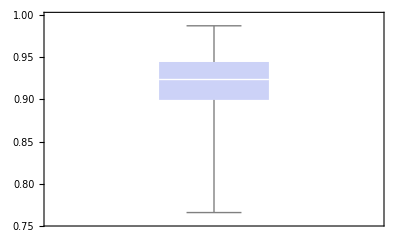

```mathematica
BC1fitness={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
BC1hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,2*gamete1[[j]]],0.5<=a<1,AppendTo[BC1hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,gamete2[[j]]]];
];
cur=Total[BC1hybrid];
AppendTo[BC1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
]
Histogram[{BC1fitness}]
BoxWhiskerChart[{BC1fitness}]
```

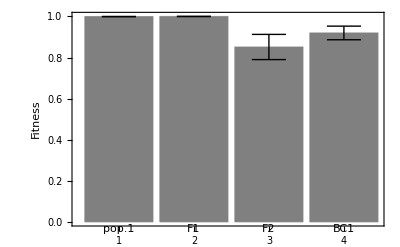

```mathematica
file={Pop1fitness,F1fitness,F2fitness,BC1fitness};
Meandata=Mean/@file
standardDev[data_]:=StandardDeviation[data]
stddevData=standardDev/@file
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
chartData=Table[Meandata[[i]]->stddevData[[i]],{i,1,Length[Meandata]}]
labels={"pop.1","F1","F2","BC1"};
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->labels,Frame->Left,FrameLabel->{None,Style["Fitness"]},ChartStyle->{Gray}]
```

## Figure 1

## Mutation size with fixations

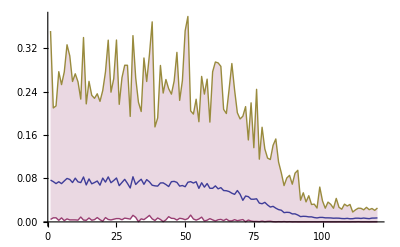

```mathematica
mutsizelist=Import["~/Desktop/FGM-master/Data sets/Figure 1/FGM_multiple100_mut=0.04_N=2000_r.dat"];
ListLinePlot[{Map[Mean,Transpose@mutsizelist],
Map[Min,Transpose@mutsizelist],
Map[Max,Transpose@mutsizelist]},PlotJoined->True,PlotRange->All,Filling->{2->{3}}]
```

## Selection coefficient with fixations

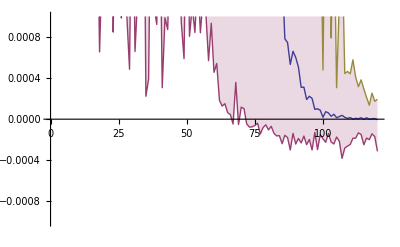

```mathematica
selcoefflist=Import["~/Desktop/FGM-master/Data sets/Figure 1/FGM_multiple100_mut=0.04_N=2000_s.dat"];
ListLinePlot[{Map[Mean,Transpose@selcoefflist],
Map[Min,Transpose@selcoefflist],
Map[Max,Transpose@selcoefflist]},PlotJoined->True,PlotRange->{{0,120},{-0.001,0.001}},Filling->{2->{3}}]
```

```mathematica
Length@selcoefflist
```

100

```mathematica
adaptationphase={};
For[i=1,i<=Length@selcoefflist,i++,
AppendTo[adaptationphase,Length@TakeWhile[Sign[selcoefflist[[i]]],#>0.5&]];
];
```

```mathematica
adaptationphase
```

{82,92,87,94,96,66,87,81,102,94,76,94,97,80,80,82,86,71,72,88,98,93,72,74,71,73,75,90,89,86,84,91,74,88,81,113,73,79,105,78,101,86,88,82,86,97,91,87,99,82,86,84,93,89,77,87,81,89,87,79,105,86,84,87,98,91,83,77,68,85,85,78,102,90,89,89,94,77,99,99,80,87,95,92,76,93,77,83,83,97,91,81,120,90,82,82,88,87,93,102}

```mathematica
N@Mean@adaptationphase
```

86.9

## Distance to the optimum along generations

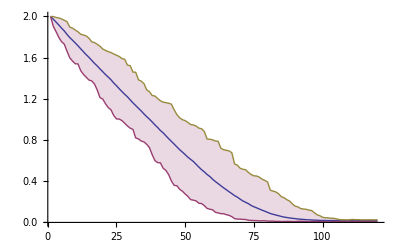

```mathematica
distoptlist=Import["~/Desktop/FGM-master/Data sets/Figure 1/FGM_multiple100_mut=0.04_N=2000_distopt.dat"];
ListLinePlot[{Map[Mean,Transpose@distoptlist],
Map[Min,Transpose@distoptlist],
Map[Max,Transpose@distoptlist]},PlotJoined->True,PlotRange->All,Filling->{2->{3}}]
```

## Waiting time with fixations

Please use the option “WorkingPrescision” when calculations by “NIntegrate” do not converge.

```mathematica
Clear["Global`*"];
M[w_,s_]:=s w(1-w);
V[w_,n_]:=w (1-w)/n;
G[x_,s_,n_]:=Exp[-Integrate[2 M[x,s]/V[x,n],x]];
u[p_,s_,n_]:=Integrate[G[x,s,n],{x,0,p}]/Integrate[G[x,s,n],{x,0,1}];
ψ[x_,s_,n_]:=2 Integrate[G[x,s,n],{x,0,1}]/(G[x,s,n]*V[x,n]);
T[p_,s_,n_]:=NIntegrate[ψ[ξ,s,n]*u[ξ,s,n](1-u[ξ,s,n]),{ξ,p,1}]+((1-u[p,s,n])/u[p,s,n])NIntegrate[ψ[ξ,s,n]*u[ξ,s,n]*u[ξ,s,n],{ξ,0,p}];

(*Parameter settings & Read file*)
q=1;
k=2;
opt1={{2,0,0,0,0,0,0,0,0,0}};
opt2={{2,0,0,0,0,0,0,0,0,0}};

scenario={1.1};
mutsize={0.04} ;
imax=10000;
n=2000;
μ=10^(-5);

For[L=1,L≤1,L++,

For[J=1,J≤1,J++,

generations={};
λ=mutsize[[J]];

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;120;;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;120;;1]];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;120;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;120;;1]];
phenotype1=Accumulate[mutpop1];
phenotype2=Accumulate[mutpop2];


Waitlist1={};
Waitlist2={};
For[gen=1,gen<Length@phenotype1,gen++,
Problist={};
AppendTo[Waitlist1,T[1/n,slistpop1[[gen]],n]]
For[i=1,i<imax,i++,
cur=phenotype1[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temp=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
curfit=Exp[-q(EuclideanDistance[cur,opt1[[L]]])^k];
tempfit=Exp[-q(EuclideanDistance[temp,opt1[[L]]])^k];
s=tempfit/curfit-1;
AppendTo[Problist,(1-Exp[-2s])/(1-Exp[-2 n s])];
];
AppendTo[Waitlist2,1/(μ*n*Mean@Problist)];
];

Waitlist3={};
Waitlist4={};
For[gen=1,gen<Length@phenotype2,gen++,
Problist={};
AppendTo[Waitlist3,T[1/n,slistpop2[[gen]],n]]
For[i=1,i<imax,i++,
cur=phenotype2[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temp=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
curfit=Exp[-q(EuclideanDistance[cur,opt2[[L]]])^k];
tempfit=Exp[-q(EuclideanDistance[temp,opt2[[L]]])^k];
s=tempfit/curfit-1;
AppendTo[Problist,(1-Exp[-2s])/(1-Exp[-2 n s])];
];
AppendTo[Waitlist4,1/(μ*n*Mean@Problist)];
];

(*Number of generations*)
AppendTo[generations,Waitlist1+Waitlist2];
AppendTo[generations,Waitlist3+Waitlist4];

];

];

];
```

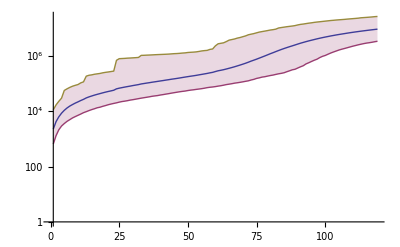

```mathematica
maxlist=Accumulate@Map[Max,Transpose[generations]];
minlist=Accumulate@Map[Min,Transpose[generations]];
meanlist=Accumulate@Map[Mean,Transpose[generations]];
ListLogPlot[{meanlist,
minlist,maxlist
},Filling->{2->{3}},Joined->True,AxesOrigin->{1,0}]
```

## Figure 2

### Haploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
Pop1fitness={};
F1fitness={};
F2fitness={};
BC1fitness={};

For[run=0,run<1,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r="<>ToString[0.04]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r="<>ToString[0.04]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;nummut2;;1]];

(*Pop1*)
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
inter=Intersection[mutpop1,mutpop1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop1,mutpop1],Intersection[mutpop1,mutpop1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop1offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop1offspring,1]];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

(*F1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];(*Calculating fitness of F1*)
];

(*F2*)
For[i=1,i≤1000,i++,
(*Making 2 F1 hybrids*)
F1hybrid1={};
F1hybrid2={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop2[[j]]]];
];

(*Making F2 hybrid*)
F2hybrid={};
inter=Intersection[F1hybrid1,F1hybrid2];(*mutations shared in both hybrids*)
comp=Complement[Union[F1hybrid1,F1hybrid2],Intersection[F1hybrid1,F1hybrid2]];(*mutations included in either hybrid*)
AppendTo[F2hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[F2hybrid,comp[[j]]]];
];

(*Calculating fitness of F2*)
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

(*BC1*)
For[i=1,i≤1000,i++,
(*Making F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC1 hybrid*)
BC1hybrid={};
inter=Intersection[F1hybrid1,mutpop1];
comp=Complement[Union[F1hybrid1,mutpop1],Intersection[F1hybrid1,mutpop1]];
AppendTo[BC1hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BC1hybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BC1hybrid];
AppendTo[BC1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

];
```

{0.998847,0.731681,0.737916,0.788242}

{1.49955×10^-14,0.101146,0.100326,0.0905563}

{0.998847→1.49955×10^-14,0.731681→0.101146,0.737916→0.100326,0.788242→0.0905563}

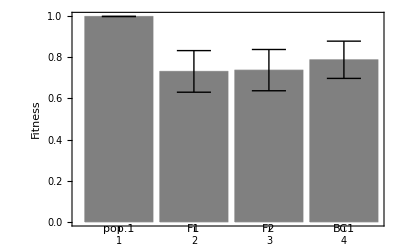

```mathematica
file={Pop1fitness,F1fitness,F2fitness,BC1fitness};
Meandata=Mean/@file
standardDev[data_]:=StandardDeviation[data]
stddevData=standardDev/@file
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
chartData=Table[Meandata[[i]]->stddevData[[i]],{i,1,Length[Meandata]}]
labels={"pop.1","F1","F2","BC1"};
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->labels,Frame->Left,FrameLabel->{None,Style["Fitness"]},ChartStyle->{Gray}]
```

```mathematica
Export["~/Desktop/Figure2_Haploid.csv",Prepend[Transpose@{Join[Pop1fitness,F1fitness,F2fitness,BC1fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1",{i,1,Length@BC1fitness,1}]]},{"Fitness","Hybrid Type"}]]
```

### Diploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
Pop1fitness={};
F1fitness={};
F2fitness={};
BC1fitness={};

For[run=0,run<1,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r="<>ToString[0.04]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r="<>ToString[0.04]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop2>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];

(*Pop1*)
gamete1=mutpop1/2;
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
(*Calculating fitness of offspring*)
cur=Total[Pop1offspring];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

(*F1*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
cur=Total[Join[gamete1,gamete2]];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];(*Calculating fitness of F1*)
];

(*F2*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
F2hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete1[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete2[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete2[[j]]]];
];
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
 ;];

(*BC1*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
BC1hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,2*gamete1[[j]]],0.5<=a<1,AppendTo[BC1hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,gamete2[[j]]]];
];
cur=Total[BC1hybrid];
AppendTo[BC1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];

];
```

```mathematica
file={Pop1fitness,F1fitness,F2fitness,BC1fitness};
Meandata=Mean/@file
standardDev[data_]:=StandardDeviation[data]
stddevData=standardDev/@file
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
chartData=Table[Meandata[[i]]->stddevData[[i]],{i,1,Length[Meandata]}]
labels={"pop.1","F1","F2","BC1"};
BarChart[chartData,ChartElementFunction->errorBar["Rectangle"],ChartLabels->labels,Frame->Left,FrameLabel->{None,Style["Fitness"]},ChartStyle->{Gray}]
```

{0.999273,0.999784,0.852461,0.921533}

{2.01051×10^-14,2.67698×10^-14,0.0632371,0.0318199}

{0.999273→2.01051×10^-14,0.999784→2.67698×10^-14,0.852461→0.0632371,0.921533→0.0318199}

```mathematica
Export["~/Desktop/Figure2_Diploid.csv",Prepend[Transpose@{Join[Pop1fitness,F1fitness,F2fitness,BC1fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1",{i,1,Length@BC1fitness,1}]]},{"Fitness","Hybrid Type"}]]
```

## Figure 3

### Haploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
mutsize={0.04,0.08,0.12} ;

Pop1fitnesslist={};
F1fitnesslist={};

For[J=1,J≤3,J++,

Pop1fitness={};
F1fitness={};
Pop1fitnessMean={};
F1fitnessMean={};

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;nummut2;;1]];

(*Pop1*)
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
inter=Intersection[mutpop1,mutpop1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop1,mutpop1],Intersection[mutpop1,mutpop1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop1offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop1offspring,1]];
AppendTo[Pop1fitness,N[Exp[-q(EuclideanDistance[cur,opt])^k],{Infinity,5}]];
];
AppendTo[Pop1fitnessMean,Mean@Pop1fitness];


(*F1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,N[Exp[-q(EuclideanDistance[cur,opt])^k],{Infinity,5}]];(*Calculating fitness of F1*)
];

AppendTo[F1fitnessMean,Mean@F1fitness]

];

AppendTo[Pop1fitnesslist,Pop1fitnessMean];
AppendTo[F1fitnesslist,F1fitnessMean];

];
```

```mathematica
Export["~/Desktop/Figure3_Haploid.csv",Prepend[Transpose@{Join[Pop1fitnesslist[[1]],Pop1fitnesslist[[2]],Pop1fitnesslist[[3]],F1fitnesslist[[1]],F1fitnesslist[[2]],F1fitnesslist[[3]]],Join[Table["Pop1small",{i,1,Length@Pop1fitnesslist[[1]],1}],Table["Pop1medium",{i,1,Length@Pop1fitnesslist[[2]],1}],Table["Pop1large",{i,1,Length@Pop1fitnesslist[[3]],1}],Table["F1small",{i,1,Length@F1fitnesslist[[1]],1}],Table["F1medium",{i,1,Length@F1fitnesslist[[2]],1}],Table["F1large",{i,1,Length@F1fitnesslist[[3]],1}]]},{"Fitness","Hybrid Type"}]];
```

### Diploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
mutsize={0.04,0.08,0.12} ;

Pop1fitnesslist={};
F2fitnesslist={};

For[J=1,J≤3,J++,

Pop1fitness={};
F2fitness={};
Pop1fitnessMean={};
F2fitnessMean={};

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r="<>ToString[mutsize[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r="<>ToString[mutsize[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop2>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];

(*Pop1*)
gamete1=mutpop1/2;
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
(*Calculating fitness of offspring*)
cur=Total[Pop1offspring];
If[Exp[-q(EuclideanDistance[cur,opt])^k]>0.02,AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]]];
];
AppendTo[Pop1fitnessMean,Mean@Pop1fitness];

(*F2*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
F2hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete1[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete2[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete2[[j]]]];
];
cur=Total[F2hybrid];
If[Exp[-q(EuclideanDistance[cur,opt])^k]>0.02,AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur,opt])^k]]];
 ];
AppendTo[F2fitnessMean,Mean@F2fitness];

];

AppendTo[Pop1fitnesslist,Pop1fitnessMean];
AppendTo[F2fitnesslist,F2fitnessMean];

];
```

```mathematica
Export["~/Desktop/Figure3_Diploid.csv",Prepend[Transpose@{Join[Pop1fitnesslist[[1]],Pop1fitnesslist[[2]],Pop1fitnesslist[[3]],F2fitnesslist[[1]],F2fitnesslist[[2]],F2fitnesslist[[3]]],Join[Table["Pop1small",{i,1,Length@Pop1fitnesslist[[1]],1}],Table["Pop1medium",{i,1,Length@Pop1fitnesslist[[2]],1}],Table["Pop1large",{i,1,Length@Pop1fitnesslist[[3]],1}],Table["F2small",{i,1,Length@F2fitnesslist[[1]],1}],Table["F2medium",{i,1,Length@F2fitnesslist[[2]],1}],Table["F2large",{i,1,Length@F2fitnesslist[[3]],1}]]},{"Fitness","Hybrid Type"}]];
```

## Figure 4

### Haploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
τ=100;(*or 50 or 20*)

Pop1fitnesslist={};
F1fitnesslist={};

For[J=1,J≤3,J++,

Pop1fitness={};
F1fitness={};
Pop1fitnessMean={};
F1fitnessMean={};

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario2."<>ToString[J]<>"_Haploid_r="<>ToString[0.04]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario2."<>ToString[J]<>"_Haploid_r="<>ToString[0.04]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
(*Renewal slist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;2*(Length@TakeWhile[Sign[slistpop1][[τ+1;;-1;;1]],#>0.5&]+τ);;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;2*(Length@TakeWhile[Sign[slistpop2][[τ+1;;-1;;1]],#>0.5&]+τ);;1]];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;2*(Length@TakeWhile[Sign[slistpop1][[τ+1;;-1;;1]],#>0.5&]+τ);;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;2*(Length@TakeWhile[Sign[slistpop2][[τ+1;;-1;;1]],#>0.5&]+τ);;1]];

(*Pop1*)
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
inter=Intersection[mutpop1,mutpop1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop1,mutpop1],Intersection[mutpop1,mutpop1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop1offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop1offspring,1]];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];
AppendTo[Pop1fitnessMean,Mean@Pop1fitness];

(*F1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];(*Calculating fitness of F1*)
];
AppendTo[F1fitnessMean,Mean@F1fitness];

];

AppendTo[Pop1fitnesslist,Pop1fitnessMean];
AppendTo[F1fitnesslist,F1fitnessMean];

];
```

```mathematica
Export["~/Desktop/Figure4_Haploid.csv",Prepend[Transpose@{Join[Pop1fitnesslist[[1]],Pop1fitnesslist[[2]],Pop1fitnesslist[[3]],F1fitnesslist[[1]],F1fitnesslist[[2]],F1fitnesslist[[3]]],Join[Table["Pop1slow",{i,1,Length@Pop1fitnesslist[[1]],1}],Table["Pop1medium",{i,1,Length@Pop1fitnesslist[[2]],1}],Table["Pop1fast",{i,1,Length@Pop1fitnesslist[[3]],1}],Table["F1slow",{i,1,Length@F1fitnesslist[[1]],1}],Table["F1medium",{i,1,Length@F1fitnesslist[[2]],1}],Table["F1fast",{i,1,Length@F1fitnesslist[[3]],1}]]},{"Fitness","Hybrid Type"}]];
```

### Diploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
τ=100;(*or 50 or 20*)

Pop1fitnesslist={};
F2fitnesslist={};


For[J=1,J≤3,J++,

Pop1fitness={};
F2fitness={};
Pop1fitnessMean={};
F2fitnessMean={};

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario2."<>ToString[J]<>"_Diploid_r="<>ToString[0.04]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario2."<>ToString[J]<>"_Diploid_r="<>ToString[0.04]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
(*adaptation phase until 10th mutations with negative coefficient after the moving optimum stopping*)
If[Length@slistpop1>2*(Length@TakeWhile[Sign[slistpop1][[τ+1;;-1;;1]],#>0.5&]+τ),nummut1=2*(Length@TakeWhile[Sign[slistpop1][[τ+1;;-1;;1]],#>0.5&]+τ),If[EvenQ@Length@slistpop1,nummut1=Length@slistpop1,nummut1=Length@slistpop1-1]];
If[Length@slistpop2>2*(Length@TakeWhile[Sign[slistpop2][[τ+1;;-1;;1]],#>0.5&]+τ),nummut2=2*(Length@TakeWhile[Sign[slistpop2][[τ+1;;-1;;1]],#>0.5&]+τ),If[EvenQ@Length@slistpop2,nummut2=Length@slistpop2,nummut2=Length@slistpop2-1]];

(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];

(*Pop1*)
gamete1=mutpop1/2;
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
(*Calculating fitness of offspring*)
cur=Total[Pop1offspring];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
];
AppendTo[Pop1fitnessMean,Mean@Pop1fitness];

(*F2*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
F2hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete1[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete2[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete2[[j]]]];
];
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];
 ;];
AppendTo[F2fitnessMean,Mean@F2fitness];

];

AppendTo[Pop1fitnesslist,Pop1fitnessMean];
AppendTo[F2fitnesslist,F2fitnessMean];

];
```

```mathematica
Export["~/Desktop/Figure4_Diploid.csv",Prepend[Transpose@{Join[Pop1fitnesslist[[1]],Pop1fitnesslist[[2]],Pop1fitnesslist[[3]],F2fitnesslist[[1]],F2fitnesslist[[2]],F2fitnesslist[[3]]],Join[Table["Pop1slow",{i,1,Length@Pop1fitnesslist[[1]],1}],Table["Pop1medium",{i,1,Length@Pop1fitnesslist[[2]],1}],Table["Pop1fast",{i,1,Length@Pop1fitnesslist[[3]],1}],Table["F2slow",{i,1,Length@F2fitnesslist[[1]],1}],Table["F2medium",{i,1,Length@F2fitnesslist[[2]],1}],Table["F2fast",{i,1,Length@F2fitnesslist[[3]],1}]]},{"Fitness","Hybrid Type"}]];
```

## Figure 5

### Haploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={{2,0,0,0,0,0,0,0,0,0},{-√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{-√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{-√2,-√2,0,0,0,0,0,0,0,0}};
scenario={1.1,3.1,3.2,3.3};
mutsize={0.04,0.08,0.12} ;

Pop1fitnesslist={};
F1fitnesslist={};

For[L=1,L≤4,L++,

For[J=1,J≤3,J++,

Pop1fitness={};
F1fitness={};
Pop1fitnessMean={};
F1fitnessMean={};

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
(*Renewal slist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;2*Length@TakeWhile[Sign[slistpop1],#>0.5&];;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;2*Length@TakeWhile[Sign[slistpop2],#>0.5&];;1]];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;2*Length@TakeWhile[Sign[slistpop1],#>0.5&];;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;2*Length@TakeWhile[Sign[slistpop2],#>0.5&];;1]];

(*Pop1*)
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
inter=Intersection[mutpop1,mutpop1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop1,mutpop1],Intersection[mutpop1,mutpop1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop1offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop1offspring,1]];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt[[L]]])^k]];
];
AppendTo[Pop1fitnessMean,Mean@Pop1fitness];

(*F1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt[[L]]])^k]];(*Calculating fitness of F1*)
];
AppendTo[F1fitnessMean,Mean@F1fitness];

];

AppendTo[Pop1fitnesslist,Pop1fitnessMean];
AppendTo[F1fitnesslist,F1fitnessMean];

];

];
```

```mathematica
Export["~/Desktop/Figure5_Haploid.csv",Prepend[Transpose@{Join[Pop1fitnesslist[[1]],Pop1fitnesslist[[2]],Pop1fitnesslist[[3]],Pop1fitnesslist[[4]],Pop1fitnesslist[[5]],Pop1fitnesslist[[6]],Pop1fitnesslist[[7]],Pop1fitnesslist[[8]],Pop1fitnesslist[[9]],Pop1fitnesslist[[10]],Pop1fitnesslist[[11]],Pop1fitnesslist[[12]],F1fitnesslist[[1]],F1fitnesslist[[2]],F1fitnesslist[[3]],F1fitnesslist[[4]],F1fitnesslist[[5]],F1fitnesslist[[6]],F1fitnesslist[[7]],F1fitnesslist[[8]],F1fitnesslist[[9]],F1fitnesslist[[10]],F1fitnesslist[[11]],F1fitnesslist[[12]]],Join[Table["Pop1small_0",{i,1,Length@Pop1fitnesslist[[1]],1}],Table["Pop1medium_0",{i,1,Length@Pop1fitnesslist[[2]],1}],Table["Pop1large_0",{i,1,Length@Pop1fitnesslist[[3]],1}],Table["Pop1small_30",{i,1,Length@Pop1fitnesslist[[4]],1}],Table["Pop1medium_30",{i,1,Length@Pop1fitnesslist[[5]],1}],Table["Pop1large_30",{i,1,Length@Pop1fitnesslist[[6]],1}],Table["Pop1small_45",{i,1,Length@Pop1fitnesslist[[7]],1}],Table["Pop1medium_45",{i,1,Length@Pop1fitnesslist[[8]],1}],Table["Pop1large_45",{i,1,Length@Pop1fitnesslist[[9]],1}],Table["Pop1small_90",{i,1,Length@Pop1fitnesslist[[10]],1}],Table["Pop1medium_90",{i,1,Length@Pop1fitnesslist[[11]],1}],Table["Pop1large_90",{i,1,Length@Pop1fitnesslist[[12]],1}],Table["F1small_0",{i,1,Length@F1fitnesslist[[1]],1}],Table["F1medium_0",{i,1,Length@F1fitnesslist[[2]],1}],Table["F1large_0",{i,1,Length@F1fitnesslist[[3]],1}],Table["F1small_30",{i,1,Length@Pop1fitnesslist[[4]],1}],Table["F1medium_30",{i,1,Length@Pop1fitnesslist[[5]],1}],Table["F1large_30",{i,1,Length@Pop1fitnesslist[[6]],1}],Table["F1small_45",{i,1,Length@Pop1fitnesslist[[7]],1}],Table["F1medium_45",{i,1,Length@Pop1fitnesslist[[8]],1}],Table["F1large_45",{i,1,Length@Pop1fitnesslist[[9]],1}],Table["F1small_90",{i,1,Length@Pop1fitnesslist[[10]],1}],Table["F1medium_90",{i,1,Length@Pop1fitnesslist[[11]],1}],Table["F1large_90",{i,1,Length@Pop1fitnesslist[[12]],1}]]},{"Fitness","Hybrid Type"}]];
```

### Diploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={{2,0,0,0,0,0,0,0,0,0},{-√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{-√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{-√2,-√2,0,0,0,0,0,0,0,0}};
scenario={1.1,3.1,3.2,3.3};
mutsize={0.04,0.08,0.12} ;

Pop1fitnesslist={};
F1fitnesslist={};

For[L=1,L≤4,L++,

For[J=1,J≤3,J++,

Pop1fitness={};
F1fitness={};

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[mutsize[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[mutsize[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop2>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];

(*Pop1*)
gamete1=mutpop1/2;
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
(*Calculating fitness of offspring*)
cur=Total[Pop1offspring];
If[Exp[-q(EuclideanDistance[cur,opt[[L]]])^k]>0.02,AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt[[L]]])^k]]];
];

(*F1*)
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
cur=Total[Join[gamete1,gamete2]];(*current position of F1 hybrid*)
If[Exp[-q(EuclideanDistance[cur,opt[[L]]])^k]>0.02,AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt[[L]]])^k]]];
];

];

AppendTo[Pop1fitnesslist,Pop1fitness];
AppendTo[F1fitnesslist,F1fitness];

];

];
```

```mathematica
Export["~/Desktop/Figure5_Diploid.csv",Prepend[Transpose@{Join[Pop1fitnesslist[[1]],Pop1fitnesslist[[2]],Pop1fitnesslist[[3]],Pop1fitnesslist[[4]],Pop1fitnesslist[[5]],Pop1fitnesslist[[6]],Pop1fitnesslist[[7]],Pop1fitnesslist[[8]],Pop1fitnesslist[[9]],Pop1fitnesslist[[10]],Pop1fitnesslist[[11]],Pop1fitnesslist[[12]],F1fitnesslist[[1]],F1fitnesslist[[2]],F1fitnesslist[[3]],F1fitnesslist[[4]],F1fitnesslist[[5]],F1fitnesslist[[6]],F1fitnesslist[[7]],F1fitnesslist[[8]],F1fitnesslist[[9]],F1fitnesslist[[10]],F1fitnesslist[[11]],F1fitnesslist[[12]]],Join[Table["Pop1small_0",{i,1,Length@Pop1fitnesslist[[1]],1}],Table["Pop1medium_0",{i,1,Length@Pop1fitnesslist[[2]],1}],Table["Pop1large_0",{i,1,Length@Pop1fitnesslist[[3]],1}],Table["Pop1small_30",{i,1,Length@Pop1fitnesslist[[4]],1}],Table["Pop1medium_30",{i,1,Length@Pop1fitnesslist[[5]],1}],Table["Pop1large_30",{i,1,Length@Pop1fitnesslist[[6]],1}],Table["Pop1small_45",{i,1,Length@Pop1fitnesslist[[7]],1}],Table["Pop1medium_45",{i,1,Length@Pop1fitnesslist[[8]],1}],Table["Pop1large_45",{i,1,Length@Pop1fitnesslist[[9]],1}],Table["Pop1small_90",{i,1,Length@Pop1fitnesslist[[10]],1}],Table["Pop1medium_90",{i,1,Length@Pop1fitnesslist[[11]],1}],Table["Pop1large_90",{i,1,Length@Pop1fitnesslist[[12]],1}],Table["F1small_0",{i,1,Length@F1fitnesslist[[1]],1}],Table["F1medium_0",{i,1,Length@F1fitnesslist[[2]],1}],Table["F1large_0",{i,1,Length@F1fitnesslist[[3]],1}],Table["F1small_30",{i,1,Length@Pop1fitnesslist[[4]],1}],Table["F1medium_30",{i,1,Length@Pop1fitnesslist[[5]],1}],Table["F1large_30",{i,1,Length@Pop1fitnesslist[[6]],1}],Table["F1small_45",{i,1,Length@Pop1fitnesslist[[7]],1}],Table["F1medium_45",{i,1,Length@Pop1fitnesslist[[8]],1}],Table["F1large_45",{i,1,Length@Pop1fitnesslist[[9]],1}],Table["F1small_90",{i,1,Length@Pop1fitnesslist[[10]],1}],Table["F1medium_90",{i,1,Length@Pop1fitnesslist[[11]],1}],Table["F1large_90",{i,1,Length@Pop1fitnesslist[[12]],1}]]},{"Fitness","Hybrid Type"}]];
```

## Figure 6

### Haploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt1={{2,0,0,0,0,0,0,0,0,0},{-√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{-√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{-√2,-√2,0,0,0,0,0,0,0,0},{-2,0,0,0,0,0,0,0,0,0}};
opt2={{2,0,0,0,0,0,0,0,0,0},{√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{√2,-√2,0,0,0,0,0,0,0,0},{2,0,0,0,0,0,0,0,0,0}};
scenario={1.1,3.1,3.2,3.3,3.4};
mutsize={0.04,0.08,0.12} ;

data1all={};
data2all={};

For[L=1,L≤5,L++,

J=1;

data1list={};
data2list={};

For[run=0,run<50,run++,
filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
(*Renewal slist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;2*Length@TakeWhile[Sign[slistpop1],#>0.5&];;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;2*Length@TakeWhile[Sign[slistpop2],#>0.5&];;1]];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;2*Length@TakeWhile[Sign[slistpop1],#>0.5&];;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;2*Length@TakeWhile[Sign[slistpop2],#>0.5&];;1]];

(*BC1 fitness in opt1*)
BC1fitness1={};
For[i=1,i≤20,i++,
(*Making 2 F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC hybrid*)
BChybrid={};
inter=Intersection[F1hybrid1,mutpop1];
comp=Complement[Union[F1hybrid1,mutpop1],Intersection[F1hybrid1,mutpop1]];
AppendTo[BChybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BChybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BChybrid];
AppendTo[BC1fitness1,Exp[-q(EuclideanDistance[cur,opt1[[L]]])^k]];
];

(*BC1 fitness in opt2*)
BC1fitness2={};
For[i=1,i≤20,i++,
(*Making 2 F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC hybrid*)
BChybrid={};
inter=Intersection[F1hybrid1,mutpop1];
comp=Complement[Union[F1hybrid1,mutpop1],Intersection[F1hybrid1,mutpop1]];
AppendTo[BChybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BChybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BChybrid];
AppendTo[BC1fitness2,Exp[-q(EuclideanDistance[cur,opt2[[L]]])^k]];
];

(*BC2 fitness in opt1*)
BC2fitness1={};
For[i=1,i≤20,i++,
(*Making 2 F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC hybrid*)
BChybrid={};
inter=Intersection[F1hybrid1,mutpop2];
comp=Complement[Union[F1hybrid1,mutpop2],Intersection[F1hybrid1,mutpop2]];
AppendTo[BChybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BChybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BChybrid];
AppendTo[BC2fitness1,Exp[-q(EuclideanDistance[cur,opt1[[L]]])^k]];
];

(*BC2 fitness in opt2*)
BC2fitness2={};
For[i=1,i≤20,i++,
(*Making 2 F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC hybrid*)
BChybrid={};
inter=Intersection[F1hybrid1,mutpop2];
comp=Complement[Union[F1hybrid1,mutpop2],Intersection[F1hybrid1,mutpop2]];
AppendTo[BChybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BChybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BChybrid];
AppendTo[BC2fitness2,Exp[-q(EuclideanDistance[cur,opt2[[L]]])^k]];
];

data1=1/2*(Mean@BC1fitness1-Mean@BC1fitness2-Mean@BC2fitness1+Mean@BC2fitness2);
data2=1/2*(Mean@BC1fitness1-Mean@BC1fitness2-Mean@BC2fitness1+Mean@BC2fitness2)/Mean@BC1fitness1;

AppendTo[data1list,data1];
AppendTo[data2list,data2];

];

AppendTo[data1all,data1list];
AppendTo[data2all,data2list];

];
```

```mathematica
Export["~/Desktop/Figure6_Haploid_01.csv",Prepend[Transpose[{Flatten[data1all],Join[Table["AE_0",{i,1,Length@data1all[[1]],1}],Table["AE_30",{i,1,Length@data1all[[2]],1}],Table["AE_45",{i,1,Length@data1all[[3]],1}],Table["AE_90",{i,1,Length@data1all[[4]],1}],Table["AE_180",{i,1,Length@data1all[[5]],1}]]}],{"Indicator","Environment"}]];

Export["~/Desktop/Figure6_Haploid_02.csv",Prepend[Transpose[{Flatten[data2all],Join[Table["AE_0",{i,1,Length@data2all[[1]],1}],Table["AE_30",{i,1,Length@data2all[[2]],1}],Table["AE_45",{i,1,Length@data2all[[3]],1}],Table["AE_90",{i,1,Length@data2all[[4]],1}],Table["AE_180",{i,1,Length@data2all[[5]],1}]]}],{"Indicator","Environment"}]];
```

### Diploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt1={{2,0,0,0,0,0,0,0,0,0},{-√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{-√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{-√2,-√2,0,0,0,0,0,0,0,0},{-2,0,0,0,0,0,0,0,0,0}};
opt2={{2,0,0,0,0,0,0,0,0,0},{√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{√2,-√2,0,0,0,0,0,0,0,0},{2,0,0,0,0,0,0,0,0,0}};
scenario={1.1,3.1,3.2,3.3,3.4};
mutsize={0.04,0.08,0.12} ;

data1all={};
data2all={};

For[L=1,L≤5,L++,

J=1;

data1list={};
data2list={};

For[run=0,run<50,run++,
filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[mutsize[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[mutsize[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop2>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];

(*BC1 in opt1*)
BC1fitness1={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤40,i++,
BC1hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,2*gamete1[[j]]],0.5<=a<1,AppendTo[BC1hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,gamete2[[j]]]];
];
cur=Total[BC1hybrid];
AppendTo[BC1fitness1,Exp[-q(EuclideanDistance[cur,opt1[[L]]])^k]];
];

(*BC1 in opt2*)
BC1fitness2={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤40,i++,
BC1hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,2*gamete1[[j]]],0.5<=a<1,AppendTo[BC1hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,gamete2[[j]]]];
];
cur=Total[BC1hybrid];
AppendTo[BC1fitness2,Exp[-q(EuclideanDistance[cur,opt2[[L]]])^k]];
];

(*BC2 fitness in opt1*)
BC2fitness1={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤40,i++,
BC2hybrid={};
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC2hybrid,2*gamete2[[j]]],0.5<=a<1,AppendTo[BC2hybrid,gamete2[[j]]]];
];
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC2hybrid,gamete1[[j]]]];
];
cur=Total[BC2hybrid];
AppendTo[BC2fitness1,Exp[-q(EuclideanDistance[cur,opt1[[L]]])^k]];
];

(*BC2 fitness in opt2*)
BC2fitness2={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤40,i++,
BC2hybrid={};
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC2hybrid,2*gamete2[[j]]],0.5<=a<1,AppendTo[BC2hybrid,gamete2[[j]]]];
];
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC2hybrid,gamete1[[j]]]];
];
cur=Total[BC2hybrid];
AppendTo[BC2fitness2,Exp[-q(EuclideanDistance[cur,opt2[[L]]])^k]];
];

data1=1/2*(Mean@BC1fitness1-Mean@BC1fitness2-Mean@BC2fitness1+Mean@BC2fitness2);
data2=1/2*(Mean@BC1fitness1-Mean@BC1fitness2-Mean@BC2fitness1+Mean@BC2fitness2)/Mean@BC1fitness1;

AppendTo[data1list,data1];
AppendTo[data2list,data2];

];

AppendTo[data1all,data1list];
AppendTo[data2all,data2list];

];
```

```mathematica
Export["~/Desktop/Figure6_Diploid_01.csv",Prepend[Transpose[{Flatten[data1all],Join[Table["AE_0",{i,1,Length@data1all[[1]],1}],Table["AE_30",{i,1,Length@data1all[[2]],1}],Table["AE_45",{i,1,Length@data1all[[3]],1}],Table["AE_90",{i,1,Length@data1all[[4]],1}],Table["AE_180",{i,1,Length@data1all[[5]],1}]]}],{"Indicator","Environment"}]];

Export["~/Desktop/Figure6_Diploid_02.csv",Prepend[Transpose[{Flatten[data2all],Join[Table["AE_0",{i,1,Length@data2all[[1]],1}],Table["AE_30",{i,1,Length@data2all[[2]],1}],Table["AE_45",{i,1,Length@data2all[[3]],1}],Table["AE_90",{i,1,Length@data2all[[4]],1}],Table["AE_180",{i,1,Length@data2all[[5]],1}]]}],{"Indicator","Environment"}]];
```

## Figure 7

### Haploid (all)

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
sphere={1,2,5,10};
trait={10,5,2,1};

Pop1fitnesslist={};
F1fitnesslist={};

For[J=1,J≤4,J++,

Pop1fitness={};
F1fitness={};
Pop1fitnessMean={};
F1fitnessMean={};

numsphere=sphere[[J]];
numtrait=trait[[J]];
optrec={};(*fixed optimum*)
For[nums=1,nums≤numsphere,nums++,
opteach={};
For[numt=1,numt≤numtrait,numt++,
If[(nums==1)&&(numt==1),AppendTo[opteach,2],AppendTo[opteach,0]];
];
AppendTo[optrec,opteach]
];

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/Figure 7/Modurality_Haploid_sphere="<>ToString[sphere[[J]]]<>"_trait="<>ToString[trait[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/Figure 7/Modurality_Haploid_sphere="<>ToString[sphere[[J]]]<>"_trait="<>ToString[trait[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
focaltraitpop1=Drop[Transpose[pop1][[4]],1];
focaltraitpop2=Drop[Transpose[pop2][[4]],1];

(*adaptation phase until mutations at the focal trait with negative coefficient*)
If[Length@slistpop1>Intersection[Flatten[Position[Sign[slistpop1],-1,1]],Flatten[Position[Sign[focaltraitpop1],1,1]]][[1]],nummut1=Intersection[Flatten[Position[Sign[slistpop1],-1,1]],Flatten[Position[Sign[focaltraitpop1],1,1]]][[1]],nummut1=Length@slistpop1];
If[Length@slistpop2>Intersection[Flatten[Position[Sign[slistpop2],-1,1]],Flatten[Position[Sign[focaltraitpop2],1,1]]][[1]],nummut2=Intersection[Flatten[Position[Sign[slistpop2],-1,1]],Flatten[Position[Sign[focaltraitpop2],1,1]]][[1]],nummut2=Length@slistpop2];

(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,3}]],1][[1;;If[nummut1*2>Length@slistpop1,Length@slistpop1,nummut1*2];;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,3}]],1][[1;;If[nummut2*2>Length@slistpop2,Length@slistpop2,nummut2*2];;1]];


muttemp1={};
muttemp2={};
For[i=1,i≤Length@mutpop1,i++,
AppendTo[muttemp1,Partition[mutpop1[[i]],numtrait]];
];
For[i=1,i≤Length@mutpop2,i++,
AppendTo[muttemp2,Partition[mutpop2[[i]],numtrait]];
];

(*Pop1*)
Pop1offspring={};
inter=Intersection[muttemp1,muttemp1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[muttemp1,muttemp1],Intersection[muttemp1,muttemp1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];

For[i=1,i≤1000,i++,
cur={};
For[nums=1,nums<=numsphere,nums++,
AppendTo[cur,Total[Transpose[Flatten[Pop1offspring,1]][[nums]]]];
];
fitnesscomp={};
For[nums=1,nums≤numsphere,nums++,
AppendTo[fitnesscomp,Exp[-q(EuclideanDistance[cur[[nums]],optrec[[nums]]])^k]];
];
AppendTo[Pop1fitness,Fold[Times,1,fitnesscomp]];
];
AppendTo[Pop1fitnessMean,Mean@Pop1fitness];

(*F1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@muttemp1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,muttemp1[[j]]]];
];
(*mutationss from population 1*)
For[j=1,j<=Length@muttemp2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,muttemp2[[j]]]];
];
cur={};
For[nums=1,nums<=numsphere,nums++,
AppendTo[cur,Total[Transpose[F1hybrid][[nums]]]];
];
fitnesscomp={};
For[nums=1,nums≤numsphere,nums++,
AppendTo[fitnesscomp,Exp[-q(EuclideanDistance[cur[[nums]],optrec[[nums]]])^k]];
];
AppendTo[F1fitness,Fold[Times,1,fitnesscomp]];
];
AppendTo[F1fitnessMean,Mean@F1fitness]

];

AppendTo[Pop1fitnesslist,Pop1fitnessMean];
AppendTo[F1fitnesslist,F1fitnessMean];

];
```

```mathematica
Export["~/Desktop/Figure7_Haploid_all.csv",Prepend[Transpose@{Join[Pop1fitnesslist[[1]],Pop1fitnesslist[[2]],Pop1fitnesslist[[3]],Pop1fitnesslist[[4]],F1fitnesslist[[1]],F1fitnesslist[[2]],F1fitnesslist[[3]],F1fitnesslist[[4]]],Join[Table["Pop1(1,10)",{i,1,Length@Pop1fitnesslist[[1]],1}],Table["Pop1(2,5)",{i,1,Length@Pop1fitnesslist[[2]],1}],Table["Pop1(5,2)",{i,1,Length@Pop1fitnesslist[[3]],1}],Table["Pop1(10,1)",{i,1,Length@Pop1fitnesslist[[4]],1}],Table["F1(1,10)",{i,1,Length@F1fitnesslist[[1]],1}],Table["F1(2,5)",{i,1,Length@F1fitnesslist[[2]],1}],Table["F1(5,2)",{i,1,Length@F1fitnesslist[[3]],1}],Table["F1(10,1)",{i,1,Length@F1fitnesslist[[4]],1}]]},{"Fitness","Hybrid Type"}]];
```

### Haploid (first half of adaptation)

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
sphere={1,2,5,10};
trait={10,5,2,1};

Pop1fitnesslist={};
F1fitnesslist={};

For[J=1,J≤4,J++,

Pop1fitness={};
F1fitness={};
Pop1fitnessMean={};
F1fitnessMean={};

numsphere=sphere[[J]];
numtrait=trait[[J]];
optrec={};(*fixed optimum*)
For[nums=1,nums≤numsphere,nums++,
opteach={};
For[numt=1,numt≤numtrait,numt++,
If[(nums==1)&&(numt==1),AppendTo[opteach,2],AppendTo[opteach,0]];
];
AppendTo[optrec,opteach]
];

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/Figure 7/Modurality_Haploid_sphere="<>ToString[sphere[[J]]]<>"_trait="<>ToString[trait[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/Figure 7/Modurality_Haploid_sphere="<>ToString[sphere[[J]]]<>"_trait="<>ToString[trait[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
focaltraitpop1=Drop[Transpose[pop1][[4]],1];
focaltraitpop2=Drop[Transpose[pop2][[4]],1];

(*adaptation phase until mutations at the focal trait with negative coefficient*)
If[Length@slistpop1>Intersection[Flatten[Position[Sign[slistpop1],-1,1]],Flatten[Position[Sign[focaltraitpop1],1,1]]][[1]],nummut1=Intersection[Flatten[Position[Sign[slistpop1],-1,1]],Flatten[Position[Sign[focaltraitpop1],1,1]]][[1]],nummut1=Length@slistpop1];
If[Length@slistpop2>Intersection[Flatten[Position[Sign[slistpop2],-1,1]],Flatten[Position[Sign[focaltraitpop2],1,1]]][[1]],nummut2=Intersection[Flatten[Position[Sign[slistpop2],-1,1]],Flatten[Position[Sign[focaltraitpop2],1,1]]][[1]],nummut2=Length@slistpop2];

If[EvenQ[nummut1],nummut1=nummut1,nummut1=nummut1+1];
If[EvenQ[nummut2],nummut2=nummut2,nummut2=nummut2+1];

(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,3}]],1][[1;;Round[nummut1*0.5];;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,3}]],1][[1;;Round[nummut2*0.5];;1]];
muttemp1={};
muttemp2={};
For[i=1,i≤Length@mutpop1,i++,
AppendTo[muttemp1,Partition[mutpop1[[i]],numtrait]];
];
For[i=1,i≤Length@mutpop2,i++,
AppendTo[muttemp2,Partition[mutpop2[[i]],numtrait]];
];

(*Pop1*)
Pop1offspring={};
inter=Intersection[muttemp1,muttemp1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[muttemp1,muttemp1],Intersection[muttemp1,muttemp1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];

For[i=1,i≤1000,i++,
cur={};
For[nums=1,nums<=numsphere,nums++,
AppendTo[cur,Total[Transpose[Flatten[Pop1offspring,1]][[nums]]]];
];
fitnesscomp={};
For[nums=1,nums≤numsphere,nums++,
AppendTo[fitnesscomp,Exp[-q(EuclideanDistance[cur[[nums]],optrec[[nums]]])^k]];
];
AppendTo[Pop1fitness,Fold[Times,1,fitnesscomp]];
];
AppendTo[Pop1fitnessMean,Mean@Pop1fitness];

(*F1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@muttemp1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,muttemp1[[j]]]];
];
(*mutationss from population 1*)
For[j=1,j<=Length@muttemp2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,muttemp2[[j]]]];
];
cur={};
For[nums=1,nums<=numsphere,nums++,
AppendTo[cur,Total[Transpose[F1hybrid][[nums]]]];
];
fitnesscomp={};
For[nums=1,nums≤numsphere,nums++,
AppendTo[fitnesscomp,Exp[-q(EuclideanDistance[cur[[nums]],optrec[[nums]]])^k]];
];
AppendTo[F1fitness,Fold[Times,1,fitnesscomp]];
];
AppendTo[F1fitnessMean,Mean@F1fitness]

];

AppendTo[Pop1fitnesslist,Pop1fitnessMean];
AppendTo[F1fitnesslist,F1fitnessMean];

];
```

```mathematica
Export["~/Desktop/Figure7_Haploid_adaptation_first.csv",Prepend[Transpose@{Join[Pop1fitnesslist[[1]],Pop1fitnesslist[[2]],Pop1fitnesslist[[3]],Pop1fitnesslist[[4]],F1fitnesslist[[1]],F1fitnesslist[[2]],F1fitnesslist[[3]],F1fitnesslist[[4]]],Join[Table["Pop1(1,10)",{i,1,Length@Pop1fitnesslist[[1]],1}],Table["Pop1(2,5)",{i,1,Length@Pop1fitnesslist[[2]],1}],Table["Pop1(5,2)",{i,1,Length@Pop1fitnesslist[[3]],1}],Table["Pop1(10,1)",{i,1,Length@Pop1fitnesslist[[4]],1}],Table["F1(1,10)",{i,1,Length@F1fitnesslist[[1]],1}],Table["F1(2,5)",{i,1,Length@F1fitnesslist[[2]],1}],Table["F1(5,2)",{i,1,Length@F1fitnesslist[[3]],1}],Table["F1(10,1)",{i,1,Length@F1fitnesslist[[4]],1}]]},{"Fitness","Hybrid Type"}]];
```

### Haploid (second half of adaptation)

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
sphere={1,2,5,10};
trait={10,5,2,1};

Pop1fitnesslist={};
F1fitnesslist={};

For[J=1,J≤4,J++,

Pop1fitness={};
F1fitness={};
Pop1fitnessMean={};
F1fitnessMean={};

numsphere=sphere[[J]];
numtrait=trait[[J]];
optrec={};(*fixed optimum*)
For[nums=1,nums≤numsphere,nums++,
opteach={};
For[numt=1,numt≤numtrait,numt++,
If[(nums==1)&&(numt==1),AppendTo[opteach,2],AppendTo[opteach,0]];
];
AppendTo[optrec,opteach]
];

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/Figure 7/Modurality_Haploid_sphere="<>ToString[sphere[[J]]]<>"_trait="<>ToString[trait[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/Figure 7/Modurality_Haploid_sphere="<>ToString[sphere[[J]]]<>"_trait="<>ToString[trait[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
focaltraitpop1=Drop[Transpose[pop1][[4]],1];
focaltraitpop2=Drop[Transpose[pop2][[4]],1];

(*adaptation phase until mutations at the focal trait with negative coefficient*)
If[Length@slistpop1>Intersection[Flatten[Position[Sign[slistpop1],-1,1]],Flatten[Position[Sign[focaltraitpop1],1,1]]][[1]],nummut1=Intersection[Flatten[Position[Sign[slistpop1],-1,1]],Flatten[Position[Sign[focaltraitpop1],1,1]]][[1]],nummut1=Length@slistpop1];
If[Length@slistpop2>Intersection[Flatten[Position[Sign[slistpop2],-1,1]],Flatten[Position[Sign[focaltraitpop2],1,1]]][[1]],nummut2=Intersection[Flatten[Position[Sign[slistpop2],-1,1]],Flatten[Position[Sign[focaltraitpop2],1,1]]][[1]],nummut2=Length@slistpop2];

If[EvenQ[nummut1],nummut1=nummut1,nummut1=nummut1+1];
If[EvenQ[nummut2],nummut2=nummut2,nummut2=nummut2+1];

(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,3}]],1][[Round[nummut1*0.5];;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,3}]],1][[Round[nummut2*0.5];;nummut2;;1]];

muttemp1={};
muttemp2={};
For[i=1,i≤Length@mutpop1,i++,
AppendTo[muttemp1,Partition[mutpop1[[i]],numtrait]];
];
For[i=1,i≤Length@mutpop2,i++,
AppendTo[muttemp2,Partition[mutpop2[[i]],numtrait]];
];

(*Pop1*)
Pop1offspring={};
inter=Intersection[muttemp1,muttemp1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[muttemp1,muttemp1],Intersection[muttemp1,muttemp1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];

For[i=1,i≤1000,i++,
cur={};
For[nums=1,nums<=numsphere,nums++,
AppendTo[cur,Total[Transpose[Flatten[Pop1offspring,1]][[nums]]]];
];
fitnesscomp={};
For[nums=1,nums≤numsphere,nums++,
AppendTo[fitnesscomp,Exp[-q(EuclideanDistance[cur[[nums]],optrec[[nums]]])^k]];
];
AppendTo[Pop1fitness,Fold[Times,1,fitnesscomp]];
];
AppendTo[Pop1fitnessMean,Mean@Pop1fitness];

(*F1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@muttemp1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,muttemp1[[j]]]];
];
(*mutationss from population 1*)
For[j=1,j<=Length@muttemp2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,muttemp2[[j]]]];
];
cur={};
For[nums=1,nums<=numsphere,nums++,
AppendTo[cur,Total[Transpose[F1hybrid][[nums]]]];
];
fitnesscomp={};
For[nums=1,nums≤numsphere,nums++,
AppendTo[fitnesscomp,Exp[-q(EuclideanDistance[cur[[nums]],optrec[[nums]]])^k]];
];
AppendTo[F1fitness,Fold[Times,1,fitnesscomp]];
];
AppendTo[F1fitnessMean,Mean@F1fitness];

];

AppendTo[Pop1fitnesslist,Pop1fitnessMean];
AppendTo[F1fitnesslist,F1fitnessMean];

];
```

```mathematica
Export["~/Desktop/Figure7_Haploid_adaptation_second.csv",Prepend[Transpose@{Join[Pop1fitnesslist[[1]],Pop1fitnesslist[[2]],Pop1fitnesslist[[3]],Pop1fitnesslist[[4]],F1fitnesslist[[1]],F1fitnesslist[[2]],F1fitnesslist[[3]],F1fitnesslist[[4]]],Join[Table["Pop1(1,10)",{i,1,Length@Pop1fitnesslist[[1]],1}],Table["Pop1(2,5)",{i,1,Length@Pop1fitnesslist[[2]],1}],Table["Pop1(5,2)",{i,1,Length@Pop1fitnesslist[[3]],1}],Table["Pop1(10,1)",{i,1,Length@Pop1fitnesslist[[4]],1}],Table["F1(1,10)",{i,1,Length@F1fitnesslist[[1]],1}],Table["F1(2,5)",{i,1,Length@F1fitnesslist[[2]],1}],Table["F1(5,2)",{i,1,Length@F1fitnesslist[[3]],1}],Table["F1(10,1)",{i,1,Length@F1fitnesslist[[4]],1}]]},{"Fitness","Hybrid Type"}]];
```

### Haploid (circling phase)

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
sphere={1,2,5,10};
trait={10,5,2,1};

Pop1fitnesslist={};
F1fitnesslist={};

For[J=1,J≤4,J++,

Pop1fitness={};
F1fitness={};
Pop1fitnessMean={};
F1fitnessMean={};

numsphere=sphere[[J]];
numtrait=trait[[J]];
optrec={};(*fixed optimum*)
For[nums=1,nums≤numsphere,nums++,
opteach={};
For[numt=1,numt≤numtrait,numt++,
If[(nums==1)&&(numt==1),AppendTo[opteach,2],AppendTo[opteach,0]];
];
AppendTo[optrec,opteach]
];

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/Figure 7/Modurality_Haploid_sphere="<>ToString[sphere[[J]]]<>"_trait="<>ToString[trait[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/Figure 7/Modurality_Haploid_sphere="<>ToString[sphere[[J]]]<>"_trait="<>ToString[trait[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
focaltraitpop1=Drop[Transpose[pop1][[4]],1];
focaltraitpop2=Drop[Transpose[pop2][[4]],1];

(*adaptation phase until mutations at the focal trait with negative coefficient*)
If[Length@slistpop1>Intersection[Flatten[Position[Sign[slistpop1],-1,1]],Flatten[Position[Sign[focaltraitpop1],1,1]]][[1]],nummut1=Intersection[Flatten[Position[Sign[slistpop1],-1,1]],Flatten[Position[Sign[focaltraitpop1],1,1]]][[1]],nummut1=Length@slistpop1];
If[Length@slistpop2>Intersection[Flatten[Position[Sign[slistpop2],-1,1]],Flatten[Position[Sign[focaltraitpop2],1,1]]][[1]],nummut2=Intersection[Flatten[Position[Sign[slistpop2],-1,1]],Flatten[Position[Sign[focaltraitpop2],1,1]]][[1]],nummut2=Length@slistpop2];

(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,3}]],1][[nummut1;;If[nummut1*2>Length@slistpop1,Length@slistpop1,nummut1*2];;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,3}]],1][[nummut2;;If[nummut2*2>Length@slistpop2,Length@slistpop2,nummut2*2];;1]];

muttemp1={};
muttemp2={};
For[i=1,i≤Length@mutpop1,i++,
AppendTo[muttemp1,Partition[mutpop1[[i]],numtrait]];
];
For[i=1,i≤Length@mutpop2,i++,
AppendTo[muttemp2,Partition[mutpop2[[i]],numtrait]];
];

(*Pop1*)
Pop1offspring={};
inter=Intersection[muttemp1,muttemp1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[muttemp1,muttemp1],Intersection[muttemp1,muttemp1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];

For[i=1,i≤1000,i++,
cur={};
For[nums=1,nums<=numsphere,nums++,
AppendTo[cur,Total[Transpose[Flatten[Pop1offspring,1]][[nums]]]];
];
fitnesscomp={};
For[nums=1,nums≤numsphere,nums++,
AppendTo[fitnesscomp,Exp[-q(EuclideanDistance[cur[[nums]],optrec[[nums]]])^k]];
];
AppendTo[Pop1fitness,Fold[Times,1,fitnesscomp]];
];
AppendTo[Pop1fitnessMean,Mean@Pop1fitness];

(*F1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@muttemp1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,muttemp1[[j]]]];
];
(*mutationss from population 1*)
For[j=1,j<=Length@muttemp2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,muttemp2[[j]]]];
];
cur={};
For[nums=1,nums<=numsphere,nums++,
AppendTo[cur,Total[Transpose[F1hybrid][[nums]]]];
];
fitnesscomp={};
For[nums=1,nums≤numsphere,nums++,
AppendTo[fitnesscomp,Exp[-q(EuclideanDistance[cur[[nums]],optrec[[nums]]])^k]];
];
AppendTo[F1fitness,Fold[Times,1,fitnesscomp]];
];
AppendTo[F1fitnessMean,Mean@F1fitness];

];

AppendTo[Pop1fitnesslist,Pop1fitnessMean];
AppendTo[F1fitnesslist,F1fitnessMean];

];
```

```mathematica
Export["~/Desktop/Figure7_Haploid_circling.csv",Prepend[Transpose@{Join[Pop1fitnesslist[[1]],Pop1fitnesslist[[2]],Pop1fitnesslist[[3]],Pop1fitnesslist[[4]],F1fitnesslist[[1]],F1fitnesslist[[2]],F1fitnesslist[[3]],F1fitnesslist[[4]]],Join[Table["Pop1(1,10)",{i,1,Length@Pop1fitnesslist[[1]],1}],Table["Pop1(2,5)",{i,1,Length@Pop1fitnesslist[[2]],1}],Table["Pop1(5,2)",{i,1,Length@Pop1fitnesslist[[3]],1}],Table["Pop1(10,1)",{i,1,Length@Pop1fitnesslist[[4]],1}],Table["F1(1,10)",{i,1,Length@F1fitnesslist[[1]],1}],Table["F1(2,5)",{i,1,Length@F1fitnesslist[[2]],1}],Table["F1(5,2)",{i,1,Length@F1fitnesslist[[3]],1}],Table["F1(10,1)",{i,1,Length@F1fitnesslist[[4]],1}]]},{"Fitness","Hybrid Type"}]];
```

## Figure 8

## (a) Mutation-order & hybrid speciation

```mathematica
Clear["Global`*"]
```

```mathematica
Solve[1-p==Exp[-p(λ*w)],p]
```

{{p→(w λ+ProductLog[-ⅇ^(-w λ) w λ])/(w λ)}}

```mathematica
pop1=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r=0.04_pop1_0.dat"];
pop2=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r=0.04_pop2_0.dat"];
```

```mathematica
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
```

```mathematica
(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;nummut2;;1]];
```

```mathematica
Pop1phenotype=Total[mutpop1];
Pop2phenotype=Total[mutpop2];
```

```mathematica
F1fitness={};
F1phenotype={};
For[i=1,i≤1000,i++,
F1hybrid={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];(*alleles from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];(*alleles from population 2*)
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];(*Calculating fitness of F1*)
AppendTo[F1phenotype,cur];
];
```

```mathematica
F1phenotype2dimension={};
For[i=1,i≤Length@F1phenotype,i++,
AppendTo[F1phenotype2dimension,F1phenotype[[i]][[1;;2;;1]]];
];
```

```mathematica
λ=5;
Parameters={};
HybridMeanEP={};
ParentMeanEP={};
For[a=0, a<4, a=a+0.02,
For[b=-2,b<2, b=b+0.02,
AppendTo[Parameters,{a,b}];
opt={a,b,0,0,0,0,0,0,0,0};
EPlist={}; (*establishment probability*)
For[i=1,i≤Length@F1phenotype,i++,
w=Exp[-q(EuclideanDistance[F1phenotype[[i]],opt])^k];
AppendTo[EPlist,(w λ+ProductLog[-ⅇ^(-w λ) w λ])/(w λ)];
];
AppendTo[HybridMeanEP,Mean[EPlist]];
w1=Exp[-q(EuclideanDistance[Pop1phenotype,opt])^k];
w2=Exp[-q(EuclideanDistance[Pop2phenotype,opt])^k];
AppendTo[ParentMeanEP,1/2(w1 λ+ProductLog[-ⅇ^(-w1 λ) w1 λ])/(w1 λ)+1/2(w2 λ+ProductLog[-ⅇ^(-w2 λ) w2 λ])/(w2 λ)];
];
];
```

```mathematica
maxratio=Table[Max[1,Max[HybridMeanEP[[i]],10^-6]/Max[ParentMeanEP[[i]],10^-6]],{i,1,Length[HybridMeanEP]}];
FinalEPPlot=Join[Parameters,Partition[Log[10,maxratio],1],2];
Show[ListDensityPlot[FinalEPPlot,InterpolationOrder->1,ColorFunction->(ColorData["LightTemperatureMap"][#/5]&),ColorFunctionScaling->False,Mesh->None,PlotRange->All],
ListPlot[F1phenotype2dimension,PlotRange->All,PlotStyle->{Black}],
ListPlot[{Pop1phenotype[[1;;2;;1]],Pop2phenotype[[1;;2;;1]]},PlotStyle->{Red, PointSize[0.03]}]]
```

-Graphics-

```mathematica
scaletable=Flatten[Table[{{1,i,i},{2,i,i}},{i,0,5,0.1}],1];ListDensityPlot[scaletable,InterpolationOrder->1,ColorFunction->(ColorData["LightTemperatureMap"][#/5]&),ColorFunctionScaling->False,Mesh->None,AspectRatio->10,FrameTicks->{None,Table[{i,10^i},{i,0,5}],None,None}]
```

-Graphics-

## (b) Mutation-order & hybrid speciation (circling optimum)

```mathematica
Clear["Global`*"]
```

```mathematica
pop1=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r=0.04_pop1_0.dat"];
pop2=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r=0.04_pop2_0.dat"];
```

```mathematica
q=1;
k=2;
opt={0,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
```

```mathematica
(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[nummut1/2;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[nummut2/2;;nummut2;;1]];
```

```mathematica
F1fitness={};
F1phenotype={};
For[i=1,i≤1000,i++,
F1hybrid={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];(*alleles from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];(*alleles from population 2*)
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt])^k]];(*Calculating fitness of F1*)
AppendTo[F1phenotype,cur];
];
```

```mathematica
Pop1phenotype=Total[mutpop1];
Pop2phenotype=Total[mutpop2];
```

```mathematica
F1phenotype2dimension={};
For[i=1,i≤Length@F1phenotype,i++,
AppendTo[F1phenotype2dimension,F1phenotype[[i]][[1;;2;;1]]];
];
```

```mathematica
λ=5;
Parameters={};
HybridMeanEP={};
ParentMeanEP={};
For[a=0, a<4, a=a+0.02,
For[b=-2,b<2, b=b+0.02,
AppendTo[Parameters,{a,b}];
opt={a,b,0,0,0,0,0,0,0,0};
EPlist={}; (*establishment probability*)
For[i=1,i≤Length@F1phenotype,i++,
w=Exp[-q(EuclideanDistance[F1phenotype[[i]],opt])^k];
AppendTo[EPlist,(w λ+ProductLog[-ⅇ^(-w λ) w λ])/(w λ)];
];
AppendTo[HybridMeanEP,Mean[EPlist]];
w1=Exp[-q(EuclideanDistance[Pop1phenotype,opt])^k];
w2=Exp[-q(EuclideanDistance[Pop2phenotype,opt])^k];
AppendTo[ParentMeanEP,1/2(w1 λ+ProductLog[-ⅇ^(-w1 λ) w1 λ])/(w1 λ)+1/2(w2 λ+ProductLog[-ⅇ^(-w2 λ) w2 λ])/(w2 λ)];
];
];
```

```mathematica
maxratio=Table[Max[1,Max[HybridMeanEP[[i]],10^-6]/Max[ParentMeanEP[[i]],10^-6]],{i,1,Length[HybridMeanEP]}];FinalEPPlot=Join[Parameters,Partition[Log[10,maxratio],1],2];
Show[ListDensityPlot[FinalEPPlot,InterpolationOrder->1,ColorFunction->(ColorData["LightTemperatureMap"][#/5]&),ColorFunctionScaling->False,Mesh->None,PlotRange->All],
ListPlot[F1phenotype2dimension,PlotRange->All,PlotStyle->{Black}],
ListPlot[{Pop1phenotype[[1;;2;;1]],Pop2phenotype[[1;;2;;1]]},PlotStyle->{Red, PointSize[0.03]}]]
```

-Graphics-

## (c) Ecological & hybrid speciation

```mathematica
Clear["Global`*"]
```

```mathematica
pop1=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario3.2_Haploid_r=0.04_pop1_0.dat"];
pop2=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario3.2_Haploid_r=0.04_pop2_0.dat"];
```

```mathematica
q=1;
k=2;
opt1={-√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0};(*fixed optimum1*)
opt2={√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0};(*fixed optimum2*)
```

```mathematica
(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;nummut2;;1]];
```

```mathematica
F1fitness={};
F1phenotype={};
For[i=1,i≤1000,i++,
F1hybrid={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];(*alleles from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];(*alleles from population 2*)
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];(*Calculating fitness of F1*)
AppendTo[F1phenotype,cur];
];
```

```mathematica
Pop1phenotype=Total[mutpop1];
Pop2phenotype=Total[mutpop2];
```

```mathematica
F1phenotype2dimension={};
For[i=1,i≤Length@F1phenotype,i++,
AppendTo[F1phenotype2dimension,F1phenotype[[i]][[1;;2;;1]]];
];
```

```mathematica
λ=5;
Parameters={};
HybridMeanEP={};
ParentMeanEP={};
For[a=-2, a<2, a=a+0.02,
For[b=-4.0,b<0.0, b=b+0.02,
AppendTo[Parameters,{a,b}];
opt={a,b,0,0,0,0,0,0,0,0};
EPlist={}; (*establishment probability*)
For[i=1,i≤Length@F1phenotype,i++,
w=Exp[-q(EuclideanDistance[F1phenotype[[i]],opt])^k];
AppendTo[EPlist,(w λ+ProductLog[-ⅇ^(-w λ) w λ])/(w λ)];
];
AppendTo[HybridMeanEP,Mean[EPlist]];
w1=Exp[-q(EuclideanDistance[Pop1phenotype,opt])^k];
w2=Exp[-q(EuclideanDistance[Pop2phenotype,opt])^k];
AppendTo[ParentMeanEP,1/2(w1 λ+ProductLog[-ⅇ^(-w1 λ) w1 λ])/(w1 λ)+1/2(w2 λ+ProductLog[-ⅇ^(-w2 λ) w2 λ])/(w2 λ)];
];
];
```

```mathematica
maxratio=Table[Max[1,Max[HybridMeanEP[[i]],10^-6]/Max[ParentMeanEP[[i]],10^-6]],{i,1,Length[HybridMeanEP]}];FinalEPPlot=Join[Parameters,Partition[Log[10,maxratio],1],2];
Show[ListDensityPlot[FinalEPPlot,InterpolationOrder->1,ColorFunction->(ColorData["LightTemperatureMap"][#/5]&),ColorFunctionScaling->False,Mesh->None,PlotRange->All],
ListPlot[F1phenotype2dimension,PlotRange->All,PlotStyle->{Black}],
ListPlot[{Pop1phenotype[[1;;2;;1]],Pop2phenotype[[1;;2;;1]]},PlotStyle->{Red, PointSize[0.03]}]]
```

-Graphics-

## (d) Ecological & hybrid speciation

```mathematica
Clear["Global`*"]
```

```mathematica
pop1=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario3.3_Haploid_r=0.04_pop1_0.dat"];
pop2=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario3.3_Haploid_r=0.04_pop2_0.dat"];
```

```mathematica
q=1;
k=2;
opt1={-√2,-√2,0,0,0,0,0,0,0,0};(*fixed optimum1*)
opt2={√2,-√2,0,0,0,0,0,0,0,0};(*fixed optimum2*)
```

```mathematica
(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;nummut2;;1]];
```

```mathematica
F1fitness={};
F1phenotype={};
For[i=1,i≤1000,i++,
F1hybrid={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];(*alleles from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];(*alleles from population 2*)
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];(*Calculating fitness of F1*)
AppendTo[F1phenotype,cur];
];
```

```mathematica
Pop1phenotype=Total[mutpop1];
Pop2phenotype=Total[mutpop2];
```

```mathematica
F1phenotype2dimension={};
For[i=1,i≤Length@F1phenotype,i++,
AppendTo[F1phenotype2dimension,F1phenotype[[i]][[1;;2;;1]]];
];
```

```mathematica
λ=5;
Parameters={};
HybridMeanEP={};
ParentMeanEP={};
For[a=-2, a<2, a=a+0.2,
For[b=-4.0,b<0.0, b=b+0.2,
AppendTo[Parameters,{a,b}];
opt={a,b,0,0,0,0,0,0,0,0};
EPlist={}; (*establishment probability*)
For[i=1,i≤Length@F1phenotype,i++,
w=Exp[-q(EuclideanDistance[F1phenotype[[i]],opt])^k];
AppendTo[EPlist,(w λ+ProductLog[-ⅇ^(-w λ) w λ])/(w λ)];
];
AppendTo[HybridMeanEP,Mean[EPlist]];
w1=Exp[-q(EuclideanDistance[Pop1phenotype,opt])^k];
w2=Exp[-q(EuclideanDistance[Pop2phenotype,opt])^k];
AppendTo[ParentMeanEP,1/2(w1 λ+ProductLog[-ⅇ^(-w1 λ) w1 λ])/(w1 λ)+1/2(w2 λ+ProductLog[-ⅇ^(-w2 λ) w2 λ])/(w2 λ)];
];
];
```

```mathematica
maxratio=Table[Max[1,Max[HybridMeanEP[[i]],10^-6]/Max[ParentMeanEP[[i]],10^-6]],{i,1,Length[HybridMeanEP]}];FinalEPPlot=Join[Parameters,Partition[Log[10,maxratio],1],2];
Show[ListDensityPlot[FinalEPPlot,InterpolationOrder->1,ColorFunction->(ColorData["LightTemperatureMap"][#/5]&),ColorFunctionScaling->False,Mesh->None,PlotRange->All],
ListPlot[F1phenotype2dimension,PlotRange->All,PlotStyle->{Black}],
ListPlot[{Pop1phenotype[[1;;2;;1]],Pop2phenotype[[1;;2;;1]]},PlotStyle->{Red, PointSize[0.03]}]]
```

-Graphics-

## Figure S2

### Haploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt1={-√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0};(*fixed optimum*)
opt2={√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0};(*fixed optimum*)
Pop1fitness={};
F1fitness={};
F2fitness={};
BC1fitnessL={};
BC1fitnessF={};
Pop2fitness={};

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario3.1_Haploid_r="<>ToString[0.04]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario3.1_Haploid_r="<>ToString[0.04]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;nummut2;;1]];

(*Pop1 in opt1*)
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
inter=Intersection[mutpop1,mutpop1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop1,mutpop1],Intersection[mutpop1,mutpop1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop1offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop1offspring,1]];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

(*F1 in opt1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];(*Calculating fitness of F1*)
];

(*F2 in opt1*)
For[i=1,i≤1000,i++,
(*Making 2 F1 hybrids*)
F1hybrid1={};
F1hybrid2={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop2[[j]]]];
];

(*Making F2 hybrid*)
F2hybrid={};
inter=Intersection[F1hybrid1,F1hybrid2];(*mutations shared in both hybrids*)
comp=Complement[Union[F1hybrid1,F1hybrid2],Intersection[F1hybrid1,F1hybrid2]];(*mutations included in either hybrid*)
AppendTo[F2hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[F2hybrid,comp[[j]]]];
];

(*Calculating fitness of F2*)
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

(*BC1 in opt1*)
For[i=1,i≤1000,i++,
(*Making F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC1 hybrid*)
BC1hybrid={};
inter=Intersection[F1hybrid1,mutpop1];
comp=Complement[Union[F1hybrid1,mutpop1],Intersection[F1hybrid1,mutpop1]];
AppendTo[BC1hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BC1hybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BC1hybrid];
AppendTo[BC1fitnessL,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

(*BC1 in opt2*)
For[i=1,i≤1000,i++,
(*Making F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC1 hybrid*)
BC1hybrid={};
inter=Intersection[F1hybrid1,mutpop1];
comp=Complement[Union[F1hybrid1,mutpop1],Intersection[F1hybrid1,mutpop1]];
AppendTo[BC1hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BC1hybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BC1hybrid];
AppendTo[BC1fitnessF,Exp[-q(EuclideanDistance[cur,opt2])^k]];
];

(*Pop2 in opt1*)
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop2offspring={};
inter=Intersection[mutpop2,mutpop2];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop2,mutpop2],Intersection[mutpop2,mutpop2]];(*mutations included in either parent*)
AppendTo[Pop2offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop2offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop2offspring,1]];
AppendTo[Pop2fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

];
```

```mathematica
Export["~/Desktop/FigureS3_Haploid.csv",Prepend[Transpose@{Join[Pop1fitness,BC1fitnessL,F1fitness,F2fitness,BC1fitnessF,Pop2fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["BC1L",{i,1,Length@BC1fitnessL,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1F",{i,1,Length@BC1fitnessF,1}],Table["Pop2",{i,1,Length@Pop2fitness,1}]]},{"Fitness","Hybrid Type"}]];
```

### Diploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt1={-√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0};(*fixed optimum*)
opt2={√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0};(*fixed optimum*)
Pop1fitness={};
F1fitness={};
F2fitness={};
BC1fitnessL={};
BC1fitnessF={};
Pop2fitness={};

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario3.1_Diploid_r="<>ToString[0.04]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario3.1_Diploid_r="<>ToString[0.04]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];

(*Pop1 in opt1*)
Pop1fitness={};
gamete1=mutpop1/2;
For[i=1,i≤20,i++,
(*Making offsprings*)
Pop1offspring={};
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
(*Calculating fitness of offspring*)
cur=Total[Pop1offspring];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

(*F1 in opt1*)
F1fitness={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤20,i++,
cur=Total[Join[gamete1,gamete2]];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];(*Calculating fitness of F1*)
];

(*F2 in opt1*)
F2fitness={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤20,i++,
F2hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete1[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete2[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete2[[j]]]];
];
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

(*BC1 in opt1*)
BC1fitnessL={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤20,i++,
BC1hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,2*gamete1[[j]]],0.5<=a<1,AppendTo[BC1hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,gamete2[[j]]]];
];
cur=Total[BC1hybrid];
AppendTo[BC1fitnessL,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

(*BC1 in opt2*)
BC1fitnessF={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤20,i++,
BC1hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,2*gamete1[[j]]],0.5<=a<1,AppendTo[BC1hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,gamete2[[j]]]];
];
cur=Total[BC1hybrid];
AppendTo[BC1fitnessF,Exp[-q(EuclideanDistance[cur,opt2])^k]];
];

(*Pop2 in opt1*)
Pop2fitness={};
gamete1=mutpop2/2;
For[i=1,i≤20,i++,
(*Making offsprings*)
Pop2offspring={};
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop2offspring,gamete1[[j]]];
];
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop2offspring,gamete1[[j]]];
];
(*Calculating fitness of offspring*)
cur=Total[Pop2offspring];
AppendTo[Pop2fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

];
```

```mathematica
Export["~/Desktop/FigureS3_Diploid.csv",Prepend[Transpose@{Join[Pop1fitness,BC1fitnessL,F1fitness,F2fitness,BC1fitnessF,Pop2fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["BC1L",{i,1,Length@BC1fitnessL,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1F",{i,1,Length@BC1fitnessF,1}],Table["Pop2",{i,1,Length@Pop2fitness,1}]]},{"Fitness","Hybrid Type"}]];
```

## Figure S3

### Haploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt1={-√2,-√2,0,0,0,0,0,0,0,0};(*fixed optimum*)
opt2={√2,-√2,0,0,0,0,0,0,0,0};(*fixed optimum*)
Pop1fitness={};
F1fitness={};
F2fitness={};
BC1fitnessL={};
BC1fitnessF={};
Pop2fitness={};

For[run=0,run<1,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario3.3_Haploid_r="<>ToString[0.04]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario3.3_Haploid_r="<>ToString[0.04]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop2>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;nummut2;;1]];


(*Pop1 in opt1*)
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
inter=Intersection[mutpop1,mutpop1];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop1,mutpop1],Intersection[mutpop1,mutpop1]];(*mutations included in either parent*)
AppendTo[Pop1offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop1offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop1offspring,1]];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

(*F1 in opt1*)
For[i=1,i≤1000,i++,
F1hybrid={};
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop1[[j]]]]
];
(*mutationss from population 1*)
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid,mutpop2[[j]]]]
];
cur=Total[F1hybrid];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];(*Calculating fitness of F1*)
];

(*F2 in opt1*)
For[i=1,i≤1000,i++,
(*Making 2 F1 hybrids*)
F1hybrid1={};
F1hybrid2={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
If[RandomReal[]<0.5,AppendTo[F1hybrid2,mutpop2[[j]]]];
];

(*Making F2 hybrid*)
F2hybrid={};
inter=Intersection[F1hybrid1,F1hybrid2];(*mutations shared in both hybrids*)
comp=Complement[Union[F1hybrid1,F1hybrid2],Intersection[F1hybrid1,F1hybrid2]];(*mutations included in either hybrid*)
AppendTo[F2hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[F2hybrid,comp[[j]]]];
];

(*Calculating fitness of F2*)
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

(*BC1 in opt1*)
For[i=1,i≤1000,i++,
(*Making F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC1 hybrid*)
BC1hybrid={};
inter=Intersection[F1hybrid1,mutpop1];
comp=Complement[Union[F1hybrid1,mutpop1],Intersection[F1hybrid1,mutpop1]];
AppendTo[BC1hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BC1hybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BC1hybrid];
AppendTo[BC1fitnessL,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

(*BC1 in opt2*)
For[i=1,i≤1000,i++,
(*Making F1 hybrids*)
F1hybrid1={};
For[j=1,j<=Length@mutpop1,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop1[[j]]]];
];
For[j=1,j<=Length@mutpop2,j++,
If[RandomReal[]<0.5,AppendTo[F1hybrid1,mutpop2[[j]]]];
];

(*Making BC1 hybrid*)
BC1hybrid={};
inter=Intersection[F1hybrid1,mutpop1];
comp=Complement[Union[F1hybrid1,mutpop1],Intersection[F1hybrid1,mutpop1]];
AppendTo[BC1hybrid,Total[inter]];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[BC1hybrid,comp[[j]]]];
];

(*Calculating fitness of BC*)
cur=Total[BC1hybrid];
AppendTo[BC1fitnessF,Exp[-q(EuclideanDistance[cur,opt2])^k]];
];

(*Pop2 in opt1*)
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop2offspring={};
inter=Intersection[mutpop2,mutpop2];(*mutations shared by parents; 100% in this case*)
comp=Complement[Union[mutpop2,mutpop2],Intersection[mutpop2,mutpop2]];(*mutations included in either parent*)
AppendTo[Pop2offspring,inter];
For[j=1,j<=Length@comp,j++,
If[RandomReal[]<0.5,AppendTo[Pop2offspring,comp[[j]]]];
];

(*Calculating fitness of offspring*)
cur=Total[Flatten[Pop2offspring,1]];
AppendTo[Pop2fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

];
```

```mathematica
Export["~/Desktop/FigureS3_Haploid.csv",Prepend[Transpose@{Join[Pop1fitness,BC1fitnessL,F1fitness,F2fitness,BC1fitnessF,Pop2fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["BC1L",{i,1,Length@BC1fitnessL,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1F",{i,1,Length@BC1fitnessF,1}],Table["Pop2",{i,1,Length@Pop2fitness,1}]]},{"Fitness","Hybrid Type"}]];
```

### Diploid

```mathematica
Clear["Global`*"];
q=1;
k=2;
opt1={-√2,-√2,0,0,0,0,0,0,0,0};(*fixed optimum*)
opt2={√2,-√2,0,0,0,0,0,0,0,0};(*fixed optimum*)
Pop1fitness={};
F1fitness={};
F2fitness={};
BC1fitnessL={};
BC1fitnessF={};
Pop2fitness={};

For[run=0,run<1,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario3.3_Diploid_r="<>ToString[0.04]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario3.3_Diploid_r="<>ToString[0.04]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=Length@slistpop1];
If[Length@slistpop2>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=Length@slistpop2];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];


(*Pop1 in opt1*)
Pop1fitness={};
gamete1=mutpop1/2;
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop1offspring={};
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop1offspring,gamete1[[j]]];
];
(*Calculating fitness of offspring*)
cur=Total[Pop1offspring];
AppendTo[Pop1fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

(*F1 in opt1*)
F1fitness={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
cur=Total[Join[gamete1,gamete2]];(*current position of F1 hybrid*)
AppendTo[F1fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];(*Calculating fitness of F1*)
];

(*F2 in opt1*)
F2fitness={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
F2hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete1[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*homozygote: 25%, heterozygote: 50%, not inherited 25%*)
Which[0<=a<0.25,AppendTo[F2hybrid,2*gamete2[[j]]],0.25<=a<0.75,AppendTo[F2hybrid,gamete2[[j]]]];
];
cur=Total[F2hybrid];
AppendTo[F2fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

(*BC1 in opt1*)
BC1fitnessL={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
BC1hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,2*gamete1[[j]]],0.5<=a<1,AppendTo[BC1hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,gamete2[[j]]]];
];
cur=Total[BC1hybrid];
AppendTo[BC1fitnessL,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

(*BC1 in opt2*)
BC1fitnessF={};
gamete1=mutpop1/2;
gamete2=mutpop2/2;
For[i=1,i≤1000,i++,
BC1hybrid={};
(*from P1 mutations*)
For[j=1,j<=Length@gamete1,j++,
a=RandomReal[];
(*homozygote: 50%, heterozygote: 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,2*gamete1[[j]]],0.5<=a<1,AppendTo[BC1hybrid,gamete1[[j]]]];
];
(*from P2 mutations*)
For[j=1,j<=Length@gamete2,j++,
a=RandomReal[];
(*heterozygote: 50%, not inherited 50%*)
Which[0<=a<0.5,AppendTo[BC1hybrid,gamete2[[j]]]];
];
cur=Total[BC1hybrid];
AppendTo[BC1fitnessF,Exp[-q(EuclideanDistance[cur,opt2])^k]];
];

(*Pop2 in opt1*)
Pop2fitness={};
gamete1=mutpop2/2;
For[i=1,i≤1000,i++,
(*Making offsprings*)
Pop2offspring={};
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop2offspring,gamete1[[j]]];
];
For[j=1,j<=Length@gamete1,j++,
AppendTo[Pop2offspring,gamete1[[j]]];
];
(*Calculating fitness of offspring*)
cur=Total[Pop2offspring];
AppendTo[Pop2fitness,Exp[-q(EuclideanDistance[cur,opt1])^k]];
];

];
```

```mathematica
Export["~/Desktop/FigureS3_Diploid.csv",Prepend[Transpose@{Join[Pop1fitness,BC1fitnessL,F1fitness,F2fitness,BC1fitnessF,Pop2fitness],Join[Table["Pop1",{i,1,Length@Pop1fitness,1}],Table["BC1L",{i,1,Length@BC1fitnessL,1}],Table["F1",{i,1,Length@F1fitness,1}],Table["F2",{i,1,Length@F2fitness,1}],Table["BC1F",{i,1,Length@BC1fitnessF,1}],Table["Pop2",{i,1,Length@Pop2fitness,1}]]},{"Fitness","Hybrid Type"}]];
```

## Table S2 Haploid

Please use the option “WorkingPrescision” when calculations by “NIntegrate” do not converge.

```mathematica
Clear["Global`*"]
```

```mathematica
M[w_,s_]:=s w(1-w);
V[w_,n_]:=w (1-w)/n;
G[x_,s_,n_]:=Exp[-Integrate[2 M[x,s]/V[x,n],x]];
u[p_,s_,n_]:=Integrate[G[x,s,n],{x,0,p}]/Integrate[G[x,s,n],{x,0,1}];
ψ[x_,s_,n_]:=2 Integrate[G[x,s,n],{x,0,1}]/(G[x,s,n]*V[x,n]);
T[p_,s_,n_]:=NIntegrate[ψ[ξ,s,n]*u[ξ,s,n](1-u[ξ,s,n]),{ξ,p,1}]+((1-u[p,s,n])/u[p,s,n])NIntegrate[ψ[ξ,s,n]*u[ξ,s,n]*u[ξ,s,n],{ξ,0,p}];
```

```mathematica
(*Parameter settings & Read file*)
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
pop1=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r=0.04_pop1_0.dat"];
pop2=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Haploid_r=0.04_pop2_0.dat"];
```

```mathematica
(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
(*Renewal slist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;2*Length@TakeWhile[Sign[slistpop1],#>0.5&];;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;2*Length@TakeWhile[Sign[slistpop2],#>0.5&];;1]];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;2*Length@TakeWhile[Sign[slistpop1],#>0.5&];;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;2*Length@TakeWhile[Sign[slistpop2],#>0.5&];;1]];
phenotype1=Accumulate[mutpop1];
phenotype2=Accumulate[mutpop2];
```

```mathematica
imax=100000;
n=2000;
λ=0.04;
μ=10^(-5);
Waitlist1={};
Waitlist2={};
For[gen=1,gen<Length@phenotype1,gen++,
Problist={};
AppendTo[Waitlist1,T[1/n,slistpop1[[gen]],n]]
For[i=1,i<imax,i++,
cur=phenotype1[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temp=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
curfit=Exp[-q(EuclideanDistance[cur,opt])^k];
tempfit=Exp[-q(EuclideanDistance[temp,opt])^k];
s=tempfit/curfit-1;
AppendTo[Problist,(1-Exp[-2s])/(1-Exp[-2 n s])];
];
AppendTo[Waitlist2,1/(μ*n*Mean@Problist)];
];
```

```mathematica
imax=100000;
n=2000;
λ=0.04;
μ=10^(-5);
Waitlist3={};
Waitlist4={};
For[gen=1,gen<Length@phenotype2,gen++,
Problist={};
AppendTo[Waitlist3,T[1/n,slistpop2[[gen]],n]]
For[i=1,i<imax,i++,
cur=phenotype2[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temp=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
curfit=Exp[-q(EuclideanDistance[cur,opt])^k];
tempfit=Exp[-q(EuclideanDistance[temp,opt])^k];
s=tempfit/curfit-1;
AppendTo[Problist,(1-Exp[-2s])/(1-Exp[-2 n s])];
];
AppendTo[Waitlist4,1/(μ*n*Mean@Problist)];
];
```

```mathematica
(*Number of fixations*)
Length@mutpop1
Length@mutpop2
(*Number of generations*)
Total[Waitlist1+Waitlist2]
Total[Waitlist3+Waitlist4]
(*% of initial phase in generations*)
Total@Part[Flatten@{Waitlist1+Waitlist2},1;;Length@mutpop1/2;;1]/Total@Flatten@{Waitlist1+Waitlist2}*100
Total@Part[Flatten@{Waitlist3+Waitlist4},1;;Length@mutpop2/2;;1]/Total@Flatten@{Waitlist3+Waitlist4}*100
```

184

176

2.29133×10^7

1.89303×10^7

8.15482

3.72067

### Scenario 1.1, 3.1~3.3

```mathematica
Clear["Global`*"];
M[w_,s_]:=s w(1-w);
V[w_,n_]:=w (1-w)/n;
G[x_,s_,n_]:=Exp[-Integrate[2 M[x,s]/V[x,n],x]];
u[p_,s_,n_]:=Integrate[G[x,s,n],{x,0,p}]/Integrate[G[x,s,n],{x,0,1}];
ψ[x_,s_,n_]:=2 Integrate[G[x,s,n],{x,0,1}]/(G[x,s,n]*V[x,n]);
T[p_,s_,n_]:=NIntegrate[ψ[ξ,s,n]*u[ξ,s,n](1-u[ξ,s,n]),{ξ,p,1}]+((1-u[p,s,n])/u[p,s,n])NIntegrate[ψ[ξ,s,n]*u[ξ,s,n]*u[ξ,s,n],{ξ,0,p}];

(*Parameter settings & Read file*)
q=1;
k=2;
opt1={{2,0,0,0,0,0,0,0,0,0},{-√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{-√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{-√2,-√2,0,0,0,0,0,0,0,0},{-2,0,0,0,0,0,0,0,0,0}};
opt2={{2,0,0,0,0,0,0,0,0,0},{√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{√2,-√2,0,0,0,0,0,0,0,0},{2,0,0,0,0,0,0,0,0,0}};

scenario={1.1,3.1,3.2,3.3};
mutsize={0.04,0.08,0.12} ;
imax=100000;
n=2000;
μ=10^(-5);

For[L=1,L≤4,L++,

For[J=1,J≤3,J++,

pop1fix={};
pop2fix={};
pop1gen={};
pop2gen={};
pop1percent={};
pop2percent={};
λ=mutsize[[J]];

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
(*Renewal slist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;2*Length@TakeWhile[Sign[slistpop1],#>0.5&];;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;2*Length@TakeWhile[Sign[slistpop2],#>0.5&];;1]];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;2*Length@TakeWhile[Sign[slistpop1],#>0.5&];;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;2*Length@TakeWhile[Sign[slistpop2],#>0.5&];;1]];
phenotype1=Accumulate[mutpop1];
phenotype2=Accumulate[mutpop2];


Waitlist1={};
Waitlist2={};
For[gen=1,gen<Length@phenotype1,gen++,
Problist={};
AppendTo[Waitlist1,T[1/n,slistpop1[[gen]],n]]
For[i=1,i<imax,i++,
cur=phenotype1[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temp=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
curfit=Exp[-q(EuclideanDistance[cur,opt1[[L]]])^k];
tempfit=Exp[-q(EuclideanDistance[temp,opt1[[L]]])^k];
s=tempfit/curfit-1;
AppendTo[Problist,(1-Exp[-2s])/(1-Exp[-2 n s])];
];
AppendTo[Waitlist2,1/(μ*n*Mean@Problist)];
];


Waitlist3={};
Waitlist4={};
For[gen=1,gen<Length@phenotype2,gen++,
Problist={};
AppendTo[Waitlist3,T[1/n,slistpop2[[gen]],n]]
For[i=1,i<imax,i++,
cur=phenotype2[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temp=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
curfit=Exp[-q(EuclideanDistance[cur,opt2[[L]]])^k];
tempfit=Exp[-q(EuclideanDistance[temp,opt2[[L]]])^k];
s=tempfit/curfit-1;
AppendTo[Problist,(1-Exp[-2s])/(1-Exp[-2 n s])];
];
AppendTo[Waitlist4,1/(μ*n*Mean@Problist)];
];


(*Number of fixations*)
AppendTo[pop1fix,Length@mutpop1];
AppendTo[pop2fix,Length@mutpop2];
(*Number of generations*)
AppendTo[pop1gen,Total[Waitlist1+Waitlist2]];
AppendTo[pop2gen,Total[Waitlist3+Waitlist4]];
(*% of initial phase in generations*)
AppendTo[pop1percent,Total@Part[Flatten@{Waitlist1+Waitlist2},1;;Length@mutpop1/2;;1]/Total@Flatten@{Waitlist1+Waitlist2}*100];
AppendTo[pop2percent,Total@Part[Flatten@{Waitlist3+Waitlist4},1;;Length@mutpop2/2;;1]/Total@Flatten@{Waitlist3+Waitlist4}*100];

];

Export["~/Desktop/TableS2_Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_alldata.csv",Transpose[{pop1fix,pop2fix,pop1gen,pop2gen,pop1percent,pop2percent}]];

Export["~/Desktop/TableS2_Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_summary.csv",{N@Mean@pop1fix,N@Mean@pop2fix,N@Mean@pop1gen,N@Mean@pop2gen,N@Mean@pop1percent,N@Mean@pop2percent,N@StandardDeviation@pop1fix,N@StandardDeviation@pop2fix,N@StandardDeviation@pop1gen,N@StandardDeviation@pop2gen,N@StandardDeviation@pop1percent,N@StandardDeviation@pop2percent,N@StandardDeviation@pop1fix/Sqrt[Length@pop1fix],N@StandardDeviation@pop2fix/Sqrt[Length@pop2fix],N@StandardDeviation@pop1gen/Sqrt[Length@pop1gen],N@StandardDeviation@pop2gen/Sqrt[Length@pop2gen],N@StandardDeviation@pop1percent/Sqrt[Length@pop1percent],N@StandardDeviation@pop2percent/Sqrt[Length@pop2percent]}];

];

];
```

### Scenario 2.1~2.3

```mathematica
Clear["Global`*"];
M[w_,s_]:=s w(1-w);
V[w_,n_]:=w (1-w)/n;
G[x_,s_,n_]:=Exp[-Integrate[2 M[x,s]/V[x,n],x]];
u[p_,s_,n_]:=Integrate[G[x,s,n],{x,0,p}]/Integrate[G[x,s,n],{x,0,1}];
ψ[x_,s_,n_]:=2 Integrate[G[x,s,n],{x,0,1}]/(G[x,s,n]*V[x,n]);
T[p_,s_,n_]:=NIntegrate[ψ[ξ,s,n]*u[ξ,s,n](1-u[ξ,s,n]),{ξ,p,1}]+((1-u[p,s,n])/u[p,s,n])NIntegrate[ψ[ξ,s,n]*u[ξ,s,n]*u[ξ,s,n],{ξ,0,p}];

(*Parameter settings & Read file*)
q=1;
k=2;

scenario={2.1,2.2,2.3};
mutsize={0.04,0.08,0.12} ;
imax=100;
n=2000;
μ=10^(-5);

For[L=1,L≤3,L++,

For[J=1,J≤1,J++,

pop1fix={};
pop2fix={};
pop1gen={};
pop2gen={};
pop1percent={};
pop2percent={};
λ=mutsize[[J]];
If[L==1,τ=100];
If[L==2,τ=50];
If[L==3,τ=20];

For[run=0,run<50,run++,

opt1={0,0,0,0,0,0,0,0,0,0};
opt2={0,0,0,0,0,0,0,0,0,0};
opt1end={2,0,0,0,0,0,0,0,0,0};
opt2end={2,0,0,0,0,0,0,0,0,0};
increment1=N@(opt1end-opt1)/τ;
increment2=N@(opt1end-opt2)/τ;

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*(Length@TakeWhile[Sign[slistpop1][[τ+1;;-1;;1]],#>0.5&]+τ),nummut1=2*(Length@TakeWhile[Sign[slistpop1][[τ+1;;-1;;1]],#>0.5&]+τ),If[EvenQ@Length@slistpop1,nummut1=Length@slistpop1,nummut1=Length@slistpop1-1]];
If[Length@slistpop2>2*(Length@TakeWhile[Sign[slistpop2][[τ+1;;-1;;1]],#>0.5&]+τ),nummut2=2*(Length@TakeWhile[Sign[slistpop2][[τ+1;;-1;;1]],#>0.5&]+τ),If[EvenQ@Length@slistpop2,nummut2=Length@slistpop2,nummut2=Length@slistpop2-1]];
(*Renewal slist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;nummut1;;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;nummut2;;1]];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,4}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,4}]],1][[1;;nummut2;;1]];
phenotype1=Accumulate[mutpop1];
phenotype2=Accumulate[mutpop2];

Waitlist1={};
Waitlist2={};

For[gen=1,gen<=τ,gen++,
Problist={};
opt1=opt1+increment1;
AppendTo[Waitlist1,T[1/n,slistpop1[[gen]],n]];
For[i=1,i<imax,i++,
cur=phenotype1[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temp=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
curfit=Exp[-q(EuclideanDistance[cur,opt1])^k];
tempfit=Exp[-q(EuclideanDistance[temp,opt1])^k];
s=tempfit/curfit-1;
AppendTo[Problist,(1-Exp[-2s])/(1-Exp[-2 n s])];
];
AppendTo[Waitlist2,1/(μ*n*Mean@Problist)];
];

For[gen=τ+1,gen<Length@phenotype1,gen++,
Problist={};
AppendTo[Waitlist1,T[1/n,slistpop1[[gen]],n]];
For[i=1,i<imax,i++,
cur=phenotype1[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temp=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
curfit=Exp[-q(EuclideanDistance[cur,opt1])^k];
tempfit=Exp[-q(EuclideanDistance[temp,opt1])^k];
s=tempfit/curfit-1;
AppendTo[Problist,(1-Exp[-2s])/(1-Exp[-2 n s])];
];
AppendTo[Waitlist2,1/(μ*n*Mean@Problist)];
];

Waitlist3={};
Waitlist4={};

For[gen=1,gen<=τ,gen++,
Problist={};
opt2=opt2+increment2;
AppendTo[Waitlist3,T[1/n,slistpop1[[gen]],n]];
For[i=1,i<imax,i++,
cur=phenotype1[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temp=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
curfit=Exp[-q(EuclideanDistance[cur,opt2])^k];
tempfit=Exp[-q(EuclideanDistance[temp,opt2])^k];
s=tempfit/curfit-1;
AppendTo[Problist,(1-Exp[-2s])/(1-Exp[-2 n s])];
];
AppendTo[Waitlist4,1/(μ*n*Mean@Problist)];
];

For[gen=τ+1,gen<Length@phenotype2,gen++,
Problist={};
AppendTo[Waitlist3,T[1/n,slistpop2[[gen]],n]]
For[i=1,i<imax,i++,
cur=phenotype2[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temp=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
curfit=Exp[-q(EuclideanDistance[cur,opt2])^k];
tempfit=Exp[-q(EuclideanDistance[temp,opt2])^k];
s=tempfit/curfit-1;
AppendTo[Problist,(1-Exp[-2s])/(1-Exp[-2 n s])];
];
AppendTo[Waitlist4,1/(μ*n*Mean@Problist)];
];

(*Number of fixations*)
AppendTo[pop1fix,Length@mutpop1];
AppendTo[pop2fix,Length@mutpop2];
(*Number of generations*)
AppendTo[pop1gen,Total[Waitlist1+Waitlist2]];
AppendTo[pop2gen,Total[Waitlist3+Waitlist4]];
(*% of initial phase in generations*)
AppendTo[pop1percent,Total@Part[Flatten@{Waitlist1+Waitlist2},1;;Length@mutpop1/2;;1]/Total@Flatten@{Waitlist1+Waitlist2}*100];
AppendTo[pop2percent,Total@Part[Flatten@{Waitlist3+Waitlist4},1;;Length@mutpop2/2;;1]/Total@Flatten@{Waitlist3+Waitlist4}*100];

];

Export["~/Desktop/TableS2_Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_alldata.csv",Transpose[{pop1fix,pop2fix,pop1gen,pop2gen,pop1percent,pop2percent}]];

Export["~/Desktop/TableS2_Scenario"<>ToString[scenario[[L]]]<>"_Haploid_r="<>ToString[mutsize[[J]]]<>"_summary.csv",{N@Mean@pop1fix,N@Mean@pop2fix,N@Mean@pop1gen,N@Mean@pop2gen,N@Mean@pop1percent,N@Mean@pop2percent,N@StandardDeviation@pop1fix,N@StandardDeviation@pop2fix,N@StandardDeviation@pop1gen,N@StandardDeviation@pop2gen,N@StandardDeviation@pop1percent,N@StandardDeviation@pop2percent,N@StandardDeviation@pop1fix/Sqrt[Length@pop1fix],N@StandardDeviation@pop2fix/Sqrt[Length@pop2fix],N@StandardDeviation@pop1gen/Sqrt[Length@pop1gen],N@StandardDeviation@pop2gen/Sqrt[Length@pop2gen],N@StandardDeviation@pop1percent/Sqrt[Length@pop1percent],N@StandardDeviation@pop2percent/Sqrt[Length@pop2percent]}];

];

];
```

## Table S2 Diploid

Please use the option “WorkingPrescision” when calculations by “NIntegrate” do not converge.

```mathematica
Clear["Global`*"]
```

```mathematica
M[w_,s_,h_]:=s w(1-w)(h+(1-2h)w);
V[w_,n_]:=w (1-w)/(2n);
G[x_,s_,h_,n_]:=Exp[-Integrate[2 M[x,s,h]/V[x,n],x]];
u[p_,s_,h_,n_]:=Integrate[G[x,s,h,n],{x,0,p}]/Integrate[G[x,s,h,n],{x,0,1}];
ψ[x_,s_,h_,n_]:=2 Integrate[G[x,s,h,n],{x,0,1}]/(G[x,s,h,n]*V[x,n]);
T[p_,s_,h_,n_]:=NIntegrate[ψ[ξ,s,h,n]*u[ξ,s,h,n](1-u[ξ,s,h,n]),{ξ,p,1}]+((1-u[p,s,h,n])/u[p,s,h,n])NIntegrate[ψ[ξ,s,h,n]*u[ξ,s,h,n]*u[ξ,s,h,n],{ξ,0,p}];
```

```mathematica
(*Parameter settings & Read file*)
q=1;
k=2;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
pop1=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r=0.08_pop1_41.dat"];
pop2=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario1.1_Diploid_r=0.08_pop2_41.dat"];
```

```mathematica
(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],If[EvenQ@Length@slistpop1,nummut1=Length@slistpop1,nummut1=Length@slistpop1-1]];
If[Length@slistpop2>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],If[EvenQ@Length@slistpop2,nummut2=Length@slistpop2,nummut2=Length@slistpop2-1]];
hlistpop1=Drop[Transpose[pop1][[3]],1];
hlistpop2=Drop[Transpose[pop2][[3]],1];
(*Renewal slist and hlist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;nummut1;;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;nummut2;;1]];
hlistpop1=Drop[Transpose[pop1][[3]],1][[1;;nummut1;;1]];
hlistpop2=Drop[Transpose[pop2][[3]],1][[1;;nummut2;;1]];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];
phenotype1=Accumulate[mutpop1];
phenotype2=Accumulate[mutpop2];
```

```mathematica
imax=100000;
n=2000;
λ=0.04;
μ=10^(-5);
Waitlist1={};
Waitlist2={};
For[gen=1,gen<Length@phenotype1,gen++,
t=T[1/n,slistpop1[[gen]],hlistpop1[[gen]],n];
AppendTo[Waitlist1,t];

Problist={};
For[i=1,i<imax,i++,
cur=phenotype1[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temphomo=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
temphetero=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]])/2;
curfit=Exp[-q(EuclideanDistance[cur,opt])^k];
temphomofit=Exp[-q(EuclideanDistance[temphomo,opt])^k];
tempheterofit=Exp[-q(EuclideanDistance[temphetero,opt])^k];
s=temphomofit/curfit-1;
h=(tempheterofit/curfit-1)/s;
AppendTo[Problist,NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1/(2 n)}]/NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1}]];
];
t=1/(μ*2n*Mean@Problist);
AppendTo[Waitlist2,t];
];
```

```mathematica
imax=100000;
n=2000;
λ=0.04;
μ=10^(-5);
Waitlist3={};
Waitlist4={};
For[gen=1,gen<Length@phenotype2,gen++,
t=T[1/n,slistpop2[[gen]],hlistpop2[[gen]],n];
AppendTo[Waitlist3,t];

Problist={};
For[i=1,i<imax,i++,
cur=phenotype2[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temphomo=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
temphetero=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]])/2;
curfit=Exp[-q(EuclideanDistance[cur,opt])^k];
temphomofit=Exp[-q(EuclideanDistance[temphomo,opt])^k];
tempheterofit=Exp[-q(EuclideanDistance[temphetero,opt])^k];
s=temphomofit/curfit-1;
h=(tempheterofit/curfit-1)/s;
AppendTo[Problist,NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1/(2 n)}]/NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1}]];
];
AppendTo[Waitlist4,1/(μ*2n*Mean@Problist)];
];
```

```mathematica
(*Number of fixations*)
Length@mutpop1
Length@mutpop2
(*Number of generations*)
Total[Waitlist1+Waitlist2]
Total[Waitlist3+Waitlist4]
(*% of initial phase in generations*)
Total@Part[Flatten@{Waitlist1+Waitlist2},1;;Length@mutpop1/2;;1]/Total@Flatten@{Waitlist1+Waitlist2}*100
Total@Part[Flatten@{Waitlist3+Waitlist4},1;;Length@mutpop2/2;;1]/Total@Flatten@{Waitlist3+Waitlist4}*100
```

124

122

5.70767×10^7

3.63773×10^7

4.22832

4.11989

### Scenario 1.1, 3.1~3.3

```mathematica
Clear["Global`*"];
M[w_,s_,h_]:=s w(1-w)(h+(1-2h)w);
V[w_,n_]:=w (1-w)/(2n);
G[x_,s_,h_,n_]:=Exp[-Integrate[2 M[x,s,h]/V[x,n],x]];
u[p_,s_,h_,n_]:=Integrate[G[x,s,h,n],{x,0,p}]/Integrate[G[x,s,h,n],{x,0,1}];
ψ[x_,s_,h_,n_]:=2 Integrate[G[x,s,h,n],{x,0,1}]/(G[x,s,h,n]*V[x,n]);
T[p_,s_,h_,n_]:=NIntegrate[ψ[ξ,s,h,n]*u[ξ,s,h,n](1-u[ξ,s,h,n]),{ξ,p,1}]+((1-u[p,s,h,n])/u[p,s,h,n])NIntegrate[ψ[ξ,s,h,n]*u[ξ,s,h,n]*u[ξ,s,h,n],{ξ,0,p}];

(*Parameter settings & Read file*)
q=1;
k=2;
opt1={{2,0,0,0,0,0,0,0,0,0},{-√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{-√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{-√2,-√2,0,0,0,0,0,0,0,0}};
opt2={{2,0,0,0,0,0,0,0,0,0},{√(2-√3),-√(2+√3),0,0,0,0,0,0,0,0},{√(2-√2),-√(2+√2),0,0,0,0,0,0,0,0},{√2,-√2,0,0,0,0,0,0,0,0}};


scenario={1.1,3.1,3.2,3.3};
mutsize={0.04,0.08,0.12} ;
imax=100000;
n=2000;
μ=10^(-5);

For[L=2,L≤4,L++,

For[J=1,J≤3,J++,

pop1fix={};
pop2fix={};
pop1gen={};
pop2gen={};
pop1percent={};
pop2percent={};
λ=mutsize[[J]];

For[run=0,run<50,run++,

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[mutsize[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[mutsize[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*Length@TakeWhile[Sign[slistpop1],#>0.5&],nummut1=2*Length@TakeWhile[Sign[slistpop1],#>0.5&],If[EvenQ@Length@slistpop1,nummut1=Length@slistpop1,nummut1=Length@slistpop1-1]];
If[Length@slistpop2>2*Length@TakeWhile[Sign[slistpop2],#>0.5&],nummut2=2*Length@TakeWhile[Sign[slistpop2],#>0.5&],If[EvenQ@Length@slistpop2,nummut2=Length@slistpop2,nummut2=Length@slistpop2-1]];
hlistpop1=Drop[Transpose[pop1][[3]],1];
hlistpop2=Drop[Transpose[pop2][[3]],1];
(*Renewal slist and hlist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;nummut1;;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;nummut2;;1]];
hlistpop1=Drop[Transpose[pop1][[3]],1][[1;;nummut1;;1]];
hlistpop2=Drop[Transpose[pop2][[3]],1][[1;;nummut2;;1]];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];
phenotype1=Accumulate[mutpop1];
phenotype2=Accumulate[mutpop2];

Waitlist1={};
Waitlist2={};
For[gen=1,gen<Length@phenotype1,gen++,
t=T[1/n,slistpop1[[gen]],hlistpop1[[gen]],n];
AppendTo[Waitlist1,t];

Problist={};
For[i=1,i<imax,i++,
cur=phenotype1[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temphomo=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
temphetero=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]])/2;
curfit=Exp[-q(EuclideanDistance[cur,opt1[[L]]])^k];
temphomofit=Exp[-q(EuclideanDistance[temphomo,opt1[[L]]])^k];
tempheterofit=Exp[-q(EuclideanDistance[temphetero,opt1[[L]]])^k];
s=temphomofit/curfit-1;
h=(tempheterofit/curfit-1)/s;
AppendTo[Problist,NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1/(2 n)}]/NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1}]];
];
t=1/(μ*2n*Mean@Problist);
AppendTo[Waitlist2,t];
];


Waitlist3={};
Waitlist4={};
For[gen=1,gen<Length@phenotype2,gen++,
t=T[1/n,slistpop2[[gen]],hlistpop2[[gen]],n];
AppendTo[Waitlist3,t];

Problist={};
For[i=1,i<imax,i++,
cur=phenotype2[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temphomo=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
temphetero=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]])/2;
curfit=Exp[-q(EuclideanDistance[cur,opt2[[L]]])^k];
temphomofit=Exp[-q(EuclideanDistance[temphomo,opt2[[L]]])^k];
tempheterofit=Exp[-q(EuclideanDistance[temphetero,opt2[[L]]])^k];
s=temphomofit/curfit-1;
h=(tempheterofit/curfit-1)/s;
AppendTo[Problist,NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1/(2 n)}]/NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1}]];
];
t=1/(μ*2n*Mean@Problist);
AppendTo[Waitlist4,t];
];

(*Number of fixations*)
AppendTo[pop1fix,Length@mutpop1];
AppendTo[pop2fix,Length@mutpop2];
(*Number of generations*)
AppendTo[pop1gen,Total[Waitlist1+Waitlist2]];
AppendTo[pop2gen,Total[Waitlist3+Waitlist4]];
(*% of initial phase in generations*)
AppendTo[pop1percent,Total@Part[Flatten@{Waitlist1+Waitlist2},1;;Length@mutpop1/2;;1]/Total@Flatten@{Waitlist1+Waitlist2}*100];
AppendTo[pop2percent,Total@Part[Flatten@{Waitlist3+Waitlist4},1;;Length@mutpop2/2;;1]/Total@Flatten@{Waitlist3+Waitlist4}*100];

];

Export["~/Desktop/TableS2_Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[mutsize[[J]]]<>"_alldata.csv",Transpose[{pop1fix,pop2fix,pop1gen,pop2gen,pop1percent,pop2percent}]];

Export["~/Desktop/TableS2_Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[mutsize[[J]]]<>"_summary.csv",{N@Mean@pop1fix,N@Mean@pop2fix,N@Mean@pop1gen,N@Mean@pop2gen,N@Mean@pop1percent,N@Mean@pop2percent,N@StandardDeviation@pop1fix,N@StandardDeviation@pop2fix,N@StandardDeviation@pop1gen,N@StandardDeviation@pop2gen,N@StandardDeviation@pop1percent,N@StandardDeviation@pop2percent,N@StandardDeviation@pop1fix/Sqrt[Length@pop1fix],N@StandardDeviation@pop2fix/Sqrt[Length@pop2fix],N@StandardDeviation@pop1gen/Sqrt[Length@pop1gen],N@StandardDeviation@pop2gen/Sqrt[Length@pop2gen],N@StandardDeviation@pop1percent/Sqrt[Length@pop1percent],N@StandardDeviation@pop2percent/Sqrt[Length@pop2percent]}];

];

];
```

### Scenario 2.1~2.3

```mathematica
Clear["Global`*"];
M[w_,s_,h_]:=s w(1-w)(h+(1-2h)w);
V[w_,n_]:=w (1-w)/(2n);
G[x_,s_,h_,n_]:=Exp[-Integrate[2 M[x,s,h]/V[x,n],x]];
u[p_,s_,h_,n_]:=Integrate[G[x,s,h,n],{x,0,p}]/Integrate[G[x,s,h,n],{x,0,1}];
ψ[x_,s_,h_,n_]:=2 Integrate[G[x,s,h,n],{x,0,1}]/(G[x,s,h,n]*V[x,n]);
T[p_,s_,h_,n_]:=NIntegrate[ψ[ξ,s,h,n]*u[ξ,s,h,n](1-u[ξ,s,h,n]),{ξ,p,1}]+((1-u[p,s,h,n])/u[p,s,h,n])NIntegrate[ψ[ξ,s,h,n]*u[ξ,s,h,n]*u[ξ,s,h,n],{ξ,0,p}];
```

```mathematica
(*Parameter settings & Read file*)
q=1;
k=2;
τ=100;
opt={2,0,0,0,0,0,0,0,0,0};(*fixed optimum*)
pop1=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario2.1_Diploid_r=0.04_pop1_41.dat"];
pop2=Import["~/Desktop/FGM-master/Data sets/All scenarios/Scenario2.1_Diploid_r=0.04_pop2_41.dat"];
```

```mathematica
(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*(Length@TakeWhile[Sign[slistpop1][[τ+1;;-1;;1]],#>0.5&]+τ),nummut1=2*(Length@TakeWhile[Sign[slistpop1][[τ+1;;-1;;1]],#>0.5&]+τ),If[EvenQ@Length@slistpop1,nummut1=Length@slistpop1,nummut1=Length@slistpop1-1]];
If[Length@slistpop2>2*(Length@TakeWhile[Sign[slistpop2][[τ+1;;-1;;1]],#>0.5&]+τ),nummut2=2*(Length@TakeWhile[Sign[slistpop2][[τ+1;;-1;;1]],#>0.5&]+τ),If[EvenQ@Length@slistpop2,nummut2=Length@slistpop2,nummut2=Length@slistpop2-1]];
hlistpop1=Drop[Transpose[pop1][[3]],1];
hlistpop2=Drop[Transpose[pop2][[3]],1];
(*Renewal slist and hlist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;nummut1;;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;nummut2;;1]];
hlistpop1=Drop[Transpose[pop1][[3]],1][[1;;nummut1;;1]];
hlistpop2=Drop[Transpose[pop2][[3]],1][[1;;nummut2;;1]];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];
phenotype1=Accumulate[mutpop1];
phenotype2=Accumulate[mutpop2];
```

```mathematica
Clear["Global`*"];
M[w_,s_,h_]:=s w(1-w)(h+(1-2h)w);
V[w_,n_]:=w (1-w)/(2n);
G[x_,s_,h_,n_]:=Exp[-Integrate[2 M[x,s,h]/V[x,n],x]];
u[p_,s_,h_,n_]:=Integrate[G[x,s,h,n],{x,0,p}]/Integrate[G[x,s,h,n],{x,0,1}];
ψ[x_,s_,h_,n_]:=2 Integrate[G[x,s,h,n],{x,0,1}]/(G[x,s,h,n]*V[x,n]);
T[p_,s_,h_,n_]:=NIntegrate[ψ[ξ,s,h,n]*u[ξ,s,h,n](1-u[ξ,s,h,n]),{ξ,p,1}]+((1-u[p,s,h,n])/u[p,s,h,n])NIntegrate[ψ[ξ,s,h,n]*u[ξ,s,h,n]*u[ξ,s,h,n],{ξ,0,p}];

(*Parameter settings & Read file*)
q=1;
k=2;

scenario={2.1,2.2,2.3};
mutsize={0.04,0.08,0.12} ;
imax=100000;
n=2000;
μ=10^(-5);

For[L=1,L≤3,L++,

For[J=1,J≤1,J++,

pop1fix={};
pop2fix={};
pop1gen={};
pop2gen={};
pop1percent={};
pop2percent={};
λ=mutsize[[J]];
If[L==1,τ=100];
If[L==2,τ=50];
If[L==3,τ=20];

For[run=0,run<50,run++,

opt1={0,0,0,0,0,0,0,0,0,0};
opt2={0,0,0,0,0,0,0,0,0,0};
opt1end={2,0,0,0,0,0,0,0,0,0};
opt2end={2,0,0,0,0,0,0,0,0,0};
increment1=N@(opt1end-opt1)/τ;
increment2=N@(opt1end-opt2)/τ;

filename1="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[mutsize[[J]]]<>"_pop1_"<>ToString[run]<>".dat";
filename2="~/Desktop/FGM-master/Data sets/All scenarios/Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[mutsize[[J]]]<>"_pop2_"<>ToString[run]<>".dat";
pop1=Import[filename1];
pop2=Import[filename2];

(*Length of adaptive & circling phase*)
(*list of selectionncoefficient*)
slistpop1=Drop[Transpose[pop1][[2]],1];
slistpop2=Drop[Transpose[pop2][[2]],1];
If[Length@slistpop1>2*(Length@TakeWhile[Sign[slistpop1][[τ+1;;-1;;1]],#>0.5&]+τ),nummut1=2*(Length@TakeWhile[Sign[slistpop1][[τ+1;;-1;;1]],#>0.5&]+τ),If[EvenQ@Length@slistpop1,nummut1=Length@slistpop1,nummut1=Length@slistpop1-1]];
If[Length@slistpop2>2*(Length@TakeWhile[Sign[slistpop2][[τ+1;;-1;;1]],#>0.5&]+τ),nummut2=2*(Length@TakeWhile[Sign[slistpop2][[τ+1;;-1;;1]],#>0.5&]+τ),If[EvenQ@Length@slistpop2,nummut2=Length@slistpop2,nummut2=Length@slistpop2-1]];
hlistpop1=Drop[Transpose[pop1][[3]],1];
hlistpop2=Drop[Transpose[pop2][[3]],1];
(*Renewal slist and hlist*)
slistpop1=Drop[Transpose[pop1][[2]],1][[1;;nummut1;;1]];
slistpop2=Drop[Transpose[pop2][[2]],1][[1;;nummut2;;1]];
hlistpop1=Drop[Transpose[pop1][[3]],1][[1;;nummut1;;1]];
hlistpop2=Drop[Transpose[pop2][[3]],1][[1;;nummut2;;1]];
(*Mutations in each population*)
mutpop1=Drop[Transpose[Drop[Transpose[pop1],{1,5}]],1][[1;;nummut1;;1]];
mutpop2=Drop[Transpose[Drop[Transpose[pop2],{1,5}]],1][[1;;nummut2;;1]];
phenotype1=Accumulate[mutpop1];
phenotype2=Accumulate[mutpop2];


Waitlist1={};
Waitlist2={};

For[gen=1,gen<=τ,gen++,
t=T[1/n,slistpop1[[gen]],hlistpop1[[gen]],n];
AppendTo[Waitlist1,t];

Problist={};
opt1=opt1+increment1;

For[i=1,i<imax,i++,
cur=phenotype1[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temphomo=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
temphetero=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]])/2;
curfit=Exp[-q(EuclideanDistance[cur,opt1])^k];
temphomofit=Exp[-q(EuclideanDistance[temphomo,opt1])^k];
tempheterofit=Exp[-q(EuclideanDistance[temphetero,opt1])^k];
s=temphomofit/curfit-1;
h=(tempheterofit/curfit-1)/s;
AppendTo[Problist,NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1/(2 n)}]/NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1}]];
];
t=1/(μ*2n*Mean@Problist);AppendTo[Waitlist2,t];
];

For[gen=τ+1,gen<Length@phenotype1,gen++,
Problist={};
t=T[1/n,slistpop1[[gen]],hlistpop1[[gen]],n];
AppendTo[Waitlist1,t];

For[i=1,i<imax,i++,
cur=phenotype1[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temphomo=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
temphetero=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]])/2;
curfit=Exp[-q(EuclideanDistance[cur,opt1])^k];
temphomofit=Exp[-q(EuclideanDistance[temphomo,opt1])^k];
tempheterofit=Exp[-q(EuclideanDistance[temphetero,opt1])^k];
s=temphomofit/curfit-1;
h=(tempheterofit/curfit-1)/s;
AppendTo[Problist,NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1/(2 n)}]/NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1}]];
];
t=1/(μ*2n*Mean@Problist);
AppendTo[Waitlist2,t];
];


Waitlist3={};
Waitlist4={};

For[gen=1,gen<=τ,gen++,
t=T[1/n,slistpop2[[gen]],hlistpop2[[gen]],n];
AppendTo[Waitlist3,t];

Problist={};
opt2=opt2+increment2;

For[i=1,i<imax,i++,
cur=phenotype2[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temphomo=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
temphetero=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]])/2;
curfit=Exp[-q(EuclideanDistance[cur,opt2])^k];
temphomofit=Exp[-q(EuclideanDistance[temphomo,opt2])^k];
tempheterofit=Exp[-q(EuclideanDistance[temphetero,opt2])^k];
s=temphomofit/curfit-1;
h=(tempheterofit/curfit-1)/s;
AppendTo[Problist,NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1/(2 n)}]/NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1}]];
];
t=1/(μ*2n*Mean@Problist);
AppendTo[Waitlist4,t];
];

For[gen=τ+1,gen<Length@phenotype2,gen++,
Problist={};
t=T[1/n,slistpop2[[gen]],hlistpop2[[gen]],n];
AppendTo[Waitlist3,t];

For[i=1,i<imax,i++,
cur=phenotype2[[gen]];
mut=Table[RandomVariate[NormalDistribution[]], {i,1,10,1}];
temphomo=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]]);
temphetero=cur+RandomVariate[ExponentialDistribution[1/λ]]*(mut/Sqrt[Total[mut^2]])/2;
curfit=Exp[-q(EuclideanDistance[cur,opt2])^k];
temphomofit=Exp[-q(EuclideanDistance[temphomo,opt2])^k];
tempheterofit=Exp[-q(EuclideanDistance[temphetero,opt2])^k];
s=temphomofit/curfit-1;
h=(tempheterofit/curfit-1)/s;
AppendTo[Problist,NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1/(2 n)}]/NIntegrate[Exp[-2n s(2h-1)x(1-x)-2n s x],{x,0,1}]];
];
t=1/(μ*2n*Mean@Problist);
AppendTo[Waitlist4,t];
];


(*Number of fixations*)
AppendTo[pop1fix,Length@mutpop1];
AppendTo[pop2fix,Length@mutpop2];
(*Number of generations*)
AppendTo[pop1gen,Total[Waitlist1+Waitlist2]];
AppendTo[pop2gen,Total[Waitlist3+Waitlist4]];
(*% of initial phase in generations*)
AppendTo[pop1percent,Total@Part[Flatten@{Waitlist1+Waitlist2},1;;Length@mutpop1/2;;1]/Total@Flatten@{Waitlist1+Waitlist2}*100];
AppendTo[pop2percent,Total@Part[Flatten@{Waitlist3+Waitlist4},1;;Length@mutpop2/2;;1]/Total@Flatten@{Waitlist3+Waitlist4}*100];

];

Export["~/Desktop/TableS2_Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[mutsize[[J]]]<>"_alldata.csv",Transpose[{pop1fix,pop2fix,pop1gen,pop2gen,pop1percent,pop2percent}]];

Export["~/Desktop/TableS2_Scenario"<>ToString[scenario[[L]]]<>"_Diploid_r="<>ToString[mutsize[[J]]]<>"_summary.csv",{N@Mean@pop1fix,N@Mean@pop2fix,N@Mean@pop1gen,N@Mean@pop2gen,N@Mean@pop1percent,N@Mean@pop2percent,N@StandardDeviation@pop1fix,N@StandardDeviation@pop2fix,N@StandardDeviation@pop1gen,N@StandardDeviation@pop2gen,N@StandardDeviation@pop1percent,N@StandardDeviation@pop2percent,N@StandardDeviation@pop1fix/Sqrt[Length@pop1fix],N@StandardDeviation@pop2fix/Sqrt[Length@pop2fix],N@StandardDeviation@pop1gen/Sqrt[Length@pop1gen],N@StandardDeviation@pop2gen/Sqrt[Length@pop2gen],N@StandardDeviation@pop1percent/Sqrt[Length@pop1percent],N@StandardDeviation@pop2percent/Sqrt[Length@pop2percent]}];

];

];
```